Last modified:  19 May 2026

# First order m-mode Effective Source

Builds the first order effective source from a λ^4 puncture in m-modes for a circular orbit 
Key features:
- Newman Penrose formalism
- comoving coordinates for a circular orbit
- m-mode decomposition

Computes the m-mode effective source from the 4th order puncture 
 for a particle on a circular orbit using comoving coordinates X^μ= (T,X,Y,Z) centered on the particle 
 X_p^μ = (T,0,0,0).  These are related to BL (t,r,θ,ϕ) coordinates by 

 T=((α+ρ_0-2)t-M √ρ_0(α^2-2α+ρ_0)ϕ)/(𝒟 ρ_0)=((a √M+√r_0 (-2 M+r_0)) t 𝒟-√M (a^2+r_0^2-2 a √(M r_0)) 𝒟 ϕ)/(2 a √M+√r0 (-3 M+r0)),

X= (r-M ρ_0)/ℬ=(r-r0)/ℬ,

Y=-Mρ_0 Cos[θ]=-r_0 Cos[θ],

Z= z_c Sin[(ϕ-Ω_p t)/2]=z_c Sin[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]
where 
ρ_0=r_0/M, α=a/(√(M r_0))
and
z_c=2 √(M/r_0)ℬ/(Ω_p 𝒟), ℬ=√((α^2+ρ_0-2)/ρ_0,), 𝒟=√((2α+ρ_0-3)/ρ_0,), Ω_p=1/(√((M α +M ρ_0)ρ_0,))

For a=0  the m-modes of the NP components are symmetric under Y->-Y and change imaginary part under m->-m

 (Adapted and truncated from  Patrick’s PunctureInCoordinates)

## Setup

```mathematica
HP = 64; (* high precision *)
GP = 16; (* global precision *)
WP = 32; (* working precision *)
Nh[f_]:=N[f,HP]
Ng[f_]:=N[f,GP]
Nw[f_]:=N[f,WP]
massval = Nh@1;
spinval = Nh@0;
```

#### Configurations (from Patrick)

##### Palettes and docked buttons

Below is the full docked buttons code. In the following sections, we explain each part.

Correcting alignment

This docked button will go through the notebook and correctly align all the text.

```mathematica
buttonalignment = With[{styles={"Section","Subsection","Subsubsection"}},
	ToBoxes@Button["align",Map[Set[CurrentValue[#,{CellMargins,1,1}],
CurrentValue[PreviousCell[#,CellStyle->styles],{CellMargins,1,1}]]&,Cells[CellStyle->"Text"]]]];
```

Correctly re-enable evaluation property

This part of the above code creates a docked button that easily allows to deactivate cell evaluation and re - enable it,
	while keeping the texts, outputs,etc default (not evaluable).  Specifically, “re-enable” in fact just sets properties back to default.

```mathematica
buttonevaluable = ToBoxes@Column[Button[StringForm["Evaluable -> ``",#], 
CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}];
```

The below code does the same thing, but it creates a palette instead. Kept it for archive purposes.

```mathematica
CreatePalette@Column[Button[StringForm["Evaluatable -> ``",#],
	CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}]
```

Full docked buttons

Implementation of each part as a docked cell. For adding new features, simply create new data as shown for the above two buttons, i.e. ToBoxes[stuff] and then put it inside the BoxData.
				The next lines shoul not be touched and their purpose is to make the toolbar expand/collapse upon clicking of the bottom panel.

```mathematica
fullDockedCellsWithCollapseToolbar=Cell[BoxData[{buttonalignment,buttonevaluable}], 
					CellFrameLabelMargins->0,CellFrameLabels->{{None,None},{ButtonBox["",
				ButtonFunction:>Function[With[{pc=ParentCell@EvaluationCell[]},SetOptions[pc,If[CurrentValue[pc,CellSize]===0,{CellSize->Inherited,CellElementSpacings->{},
				CellFrameMargins->Inherited},{CellSize->0,CellElementSpacings->{"CellMinHeight"->0},CellFrameMargins->0}]]]], ImageSize->{Scaled[2],15},Evaluator->Automatic],None}}];
				SetOptions[EvaluationNotebook[],DockedCells->fullDockedCellsWithCollapseToolbar]
				Clear[buttonalignment,buttonevaluable]
```

## Preamble

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$DefInfoQ=False;
$CVVerbose=False;
```

```mathematica
$PrePrint = ScreenDollarIndices;
```

```mathematica
$CovDFormat="Postfix";
```

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->None]
```

{Verbose→False,UseMetricOnVBundle→None,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

```mathematica
SetOptions[Parallelize,Method->"FinestGrained"]
```

{DistributedContexts:>$Context,Method→FinestGrained,ProgressReporting:>$ProgressReporting}

```mathematica
SetOptions[ParallelMap,Method->"FinestGrained"]
```

{DistributedContexts:>$DistributedContexts,Method→FinestGrained,ProgressReporting:>$ProgressReporting}

```mathematica
org[expr_]:=ToCanonical[ContractMetric[expr,OverDerivatives->True]//CheckZeroDerivative,UseMetricOnVBundle->All]
```

## Manifolds, Coordinates, Metrics

```mathematica
DefManifold[M4,4,{α2,β2,γ2,μ2,ν2,ρ2,υ2,ι2,σ2,ζ2,ξ2,χ2}]
```

#### Constants

```mathematica
DefConstantSymbol[λ]
DefConstantSymbol[m] (* mode number *)
DefConstantSymbol[M] (* Kerr Mass *)
DefConstantSymbol[r0] (* constant particle radius *)
DefConstantSymbol[{a,ℬ,𝒟,zc,α,ρ0,Ω}] (* quantities eval'd at the particle *)
```

#### Coordinate Chart

```mathematica
DefChart[CM,M4,{0,1,2,3},{T[],X[],Y[],Z[]},ChartColor->Red] (* local coordinates centered  to the particle *)
```

```mathematica
DefChart[BL,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Blue] (* local coordinates centered on the Kerr BH *)
```

```mathematica
OnPart={X[]->0,Y[]->0,Z[]->0}; (* limit to the particle *)
```

```mathematica
(* aux  quantities in the coordinate transformation between X and x *)
myzc = 2(√M)/(√r0)ℬ/(Ω 𝒟)/.r0->ρ0 M//PowerExpand;
𝒟expr  =(√(2α+ρ0-3))/(√ρ0);
ℬexpr = (√(α^2+ρ0-2))/(√ρ0);
Ωexpr=1/(√ρ0 M(α+ρ0));
```

```mathematica
BDzcRules={zc->myzc,ℬ->ℬexpr,𝒟->𝒟expr,Ω->Ωexpr};
```

```mathematica
SchWLimit={α->0,a->0};
BDzcRules$SchWLimit=BDzcRules//.SchWLimit//Simplify;
```

```mathematica
ToVars={r0->M ρ0,a->α √M √r0};
```

```mathematica
$Assumptions={r0,M,a,α,Ω,ℬ,𝒟,zc,R[],X[],Y[],Z[]}∈Reals&&zc>0&&𝒟>0&&ℬ>0&&Ω>0&&ρ0>0&&M>0&&0<a<1&&0<α<1&&R[]>0&&-zc<=Z[]<=zc&&X[]!=0&&-M ρ0<=Y[]<=M ρ0 && X[] ∈ Reals && X ∈ Reals;
```

```mathematica
(* α and ρ0 are dimensionless *)
αρ0Toar0$Rule = {α -> a r0^(-1/2) M^(-1/2) ,ρ0 -> r0/M};
𝒳𝒴𝒵ToXYZ$Rule = {𝒳 ->( ℬ/r0) X[]+1 ,  𝒴 ->Y[]/r0 , 𝒵 -> (ℬ*ρ0^(5/2)*Sqrt[zc^2-Z[]^2])/zc}/.ToVars;
```

```mathematica
zc//.BDzcRules//.αρ0Toar0$Rule
```

(2 M √(-2+a^2/(M r0)+r0/M) (a/(√M √r0)+r0/M))/(√(-3+(2 a)/(√M √r0)+r0/M))

```mathematica
αρToℬ={-2+α^2+ρ0->ℬ^2 ρ0};
αρTo𝒟={(-3+2 α+ρ0)->𝒟^2 ρ0};
apToBD=Join[αρToℬ,αρTo𝒟,{(α+ρ0)->(zc 𝒟)/(2 M ℬ)}];
```

#### Metric functions

```mathematica
metric$InTXYZCoordinates = ({{-(𝒴^4 α^4+𝒳^4 (-1+𝒴^2) ρ0^2+𝒴^2 α^2 ρ0 (2 α+ρ0)-2 𝒳 (𝒴^2 α+ρ0)^2+𝒳^2 ρ0 (𝒴^4 α^2+ρ0 (2 α+ρ0)))/(ρ0 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0)), 0, 0, (ρ0 (-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)+2 𝒳 (𝒴^2 α+ρ0) (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))-𝒴^2 α^2 (ρ0 (-α+ρ0)+𝒴^2 α^2 (-2+α+ρ0))-𝒳^2 ρ0 (ρ0 (-α+ρ0)+𝒴^4 α^2 (-2+α+ρ0))))/(𝒵 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))}, {0, ((-2+α^2+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))/(ρ0 (α^2+𝒳 (-2+𝒳 ρ0))), 0, 0}, {0, 0, (𝒴^2 α^2+𝒳^2 ρ0)/(ρ0-𝒴^2 ρ0), 0}, {(ρ0 (-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)+2 𝒳 (𝒴^2 α+ρ0) (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))-𝒴^2 α^2 (ρ0 (-α+ρ0)+𝒴^2 α^2 (-2+α+ρ0))-𝒳^2 ρ0 (ρ0 (-α+ρ0)+𝒴^4 α^2 (-2+α+ρ0))))/(𝒵 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0)), 0, 0, (ρ0^3 (-𝒴^4 α^4 (-2+α+ρ0)^2-𝒳^4 (-1+𝒴^2) ρ0^2 (-2+α+ρ0)^2+2 𝒳 (ρ0-α ρ0+𝒴^2 α (-2+α+ρ0))^2+𝒴^2 (-1+α) α^2 ρ0 (ρ0+α (-4+2 α+ρ0))+𝒳^2 ρ0 (-𝒴^4 α^2 (-2+α+ρ0)^2+(-1+α) ρ0 (ρ0+α (-4+2 α+ρ0)))))/(𝒵^2 (-3+2 α+ρ0) (𝒴^2 α^2+𝒳^2 ρ0))}})//.{α^2+ρ0-2->ℬ^2 ρ0,2α+ρ0-3->𝒟^2 ρ0};
```

```mathematica
metricSimp=((metric$InTXYZCoordinates/.𝒳𝒴𝒵ToXYZ$Rule/.ToVars//Simplify//PowerExpand)/.(1-Z[]^2/zc^2)^(n_.):>((zc^2-Z[]^2)^n)/((zc^2)^n)//PowerExpand)//.apToBD//Simplify;
```

```mathematica
metricCM=CTensor[metricSimp,{-CM,-CM}];
```

```mathematica
SetCMetric[metricCM,CM,SignatureOfMetric->{3,1,0}]
```

```mathematica
CDCM=CovDOfMetric[metricCM];
```

#### Chart conversion

```mathematica
TXYZCoordinates = {T[]->((a √M+√r0 (-2 M+r0)) t[] 𝒟-√M (a^2+r0^2-2 a √(M r0)) 𝒟 ϕ[])/(2 a √M+√r0 (-3 M+r0)),X[]->(r[]-r0)/ℬ,Y[]->-r0 Cos[θ[]],Z[]->zc Sin[1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])]};
```

```mathematica
MixedCoordinatesTransform={R[]->√(X[]^2+Y[]^2+Z[]^2),X[]->ℬ^-1(r[]-M ρ0),Y[]->-M ρ0 Cos[θ[]],Zp[]->zc Sin[ϕ[]],Z[]->zc Sin[ϕ[]/2],ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(ϱ[]^2+zc^2/2)/(ϱ[] √(ϱ[]^2+zc^2))};
```

```mathematica
ϱℛzToXY={ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))};
ϱℛzToXθ={ℛ[]->√(zc^2+ϱ[]^2),ϱ[]->√(X[]^2+Y[]^2),z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))}//.Y[]->-r0 Cos[θ[]];
XYtoBL={X[]->(r[]-r0)/ℬ,Y[]->-r0 Cos[θ[]]};
XtoBL=X[]->(r[]-r0)/ℬ;
YtoBL=Y[]->-r0 Cos[θ[]];
ZtoBL=Z[]->zc Sin[1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])];
ztoBL=z[]->(X[]^2+Y[]^2+zc^2/2)/(√(X[]^2+Y[]^2)√(X[]^2+Y[]^2+zc^2))/.XYtoBL;
```

#### Comoving Tetrad Basis

```mathematica
Map[PDCM[-α2],TXYZCoordinates,{2}]
```

{e |   | 0
α2 |  →((a √M+√r0 (-2 M+r0)) 𝒟 e |   | 0
α2 |  -√M (a^2+r0^2-2 a √(M r0)) 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0)),e |   | 1
α2 |  →(e |   | 1
α2 |)/ℬ,e |   | 2
α2 |  →r0 e |   | 2
α2 |   Sin[θ],e |   | 3
α2 |  →1/2 zc (-(√M e |   | 0
α2 |)/(a √M+r0^(3/2))+e |   | 3
α2 |  ) Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}

```mathematica
Map[ToBasis[BL],%,{2}]
```

{e |   | 0
α2 |  →(a √M 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))-(2 M √r0 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))+(r0^(3/2) 𝒟 e |   | 0
α2 |)/(2 a √M+√r0 (-3 M+r0))-(a^2 √M 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0))-(√M r0^2 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0))+(2 a √M √(M r0) 𝒟 e |   | 3
α2 |)/(2 a √M+√r0 (-3 M+r0)),e |   | 1
α2 |  →(e |   | 1
α2 |)/ℬ,e |   | 2
α2 |  →r0 e |   | 2
α2 |   Sin[θ],e |   | 3
α2 |  →-(√M zc e |   | 0
α2 |   Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))+1/2 zc e |   | 3
α2 |   Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}

```mathematica
%//ComponentArray//Simplify
```

{{e |   | 0
0 |  →((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),e |   | 0
1 |  →0,e |   | 0
2 |  →0,e |   | 0
3 |  →-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0))},{e |   | 1
0 |  →0,e |   | 1
1 |  →1/ℬ,e |   | 1
2 |  →0,e |   | 1
3 |  →0},{e |   | 2
0 |  →0,e |   | 2
1 |  →0,e |   | 2
2 |  →r0 Sin[θ],e |   | 2
3 |  →0},{e |   | 3
0 |  →-(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2))),e |   | 3
1 |  →0,e |   | 3
2 |  →0,e |   | 3
3 |  →1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}}

```mathematica
%/.Rule->ComponentValue;
```

#### Coordinate Jacobian

```mathematica
jacobianmatrix=ToValues@ComponentArray@Basis[-{α2,BL},{β2,CM}]
```

{{((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),0,0,-(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))},{0,1/ℬ,0,0},{0,0,r0 Sin[θ],0},{-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),0,0,1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}}

```mathematica
jacobianmatrix//MatrixForm
```

(((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)) | 0 | 0 | -(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))
0 | 1/ℬ | 0 | 0
0 | 0 | r0 Sin[θ] | 0
-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)) | 0 | 0 | 1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])

```mathematica
?SetBasisChange
```

```mathematica
SetBasisChange[CTensor[jacobianmatrix,{-BL,CM}],BL]; (* (∂X)/(∂x) indices?? how does this transform from CM to BL, for instance does it transform covariant or contravariant indices? *)
```

```mathematica
TrigArgToZ=1/2 (-(√M t[])/(a √M+r0^(3/2))+ϕ[])->ArcSin[Z[]/zc];
```

## Kinnersley tetrad

#### Transformation and definitions

```mathematica
KerrVals={Σ->r[]^2+a^2 Cos[θ[]]^2,Δ->r[]^2-2M r[]+a^2,ζ->r[]-I a Cos[θ[]],ζb->r[]+I a Cos[θ[]]};
```

```mathematica
BLtoCM={r[]->ℬ X[]+r0,Cos[θ[]]->Y[]/-r0,Sin[θ[]]->PowerExpand[Together[Sin[ArcCos[Y[]/-r0]]]],Csc[θ[]]->1/PowerExpand[Together[Sin[ArcCos[Y[]/-r0]]]],Cos[1/2 (-(√M t)/(a √M+Subscript[r, 0]^(3/2))+ϕ)]->PowerExpand[Together[Cos[ArcSin[Z[]/zc]]]],Cos[1/2 ((√M t)/(a √M+r0^(3/2))-ϕ)]->PowerExpand[Together[Cos[ArcSin[Z[]/zc]]]]};
```

#### BL tetrad legs

```mathematica
lBL=CTensor[(PowerExpand[√((2Σ)/Δ)1/(√(2Δ Σ))]{r[]^2+a^2,Δ,0,a}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
nBL=CTensor[(PowerExpand[(√Δ)/(√(2Σ))1/(√(2Δ Σ))]{r[]^2+a^2,-Δ,0,a}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
mBL=CTensor[((√Σ)/ζb 1/(√(2Σ)){I a Sin[θ[]],0,1,I/Sin[θ[]]}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
mBarBL=CTensor[((√Σ)/ζ 1/(√(2Σ)){-I a Sin[θ[]],0,1,-I/Sin[θ[]]}/.KerrVals/.BLtoCM//.ToVars/.apToBD//FullSimplify)/.apToBD//FullSimplify,{BL}];
```

```mathematica
BLtoCM
```

{r→r0+ℬ X,Cos[θ]→-Y/r0,Sin[θ]→(√(r0^2-Y^2))/r0,Csc[θ]→r0/(√(r0^2-Y^2)),Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]→(√(zc^2-Z^2))/zc,Cos[1/2 ((√M t)/(a √M+r0^(3/2))-ϕ)]→(√(zc^2-Z^2))/zc}

#### Comoving tetrad Legs

```mathematica
lCM=(ToCTensor[lBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
nCM=(ToCTensor[nBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
mCM=(ToCTensor[mBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
mBarCM=(ToCTensor[mBarBL,{CM}]//.BLtoCM//.ToVars//FullSimplify)//.apToBD//Expand//FullSimplify;
```

```mathematica
jacobianmatrix
```

{{((a √M+√r0 (-2 M+r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),0,0,-(√M zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)])/(2 (a √M+r0^(3/2)))},{0,1/ℬ,0,0},{0,0,r0 Sin[θ],0},{-(√M (a^2+r0^2-2 a √(M r0)) 𝒟)/(2 a √M+√r0 (-3 M+r0)),0,0,1/2 zc Cos[1/2 (-(√M t)/(a √M+r0^(3/2))+ϕ)]}}

## h^S1 puncture and Teff

### Define Tetrad components

#### Define coefficients

Label indices: (R power, X power, Y power, Z power)

```mathematica
(* coefficients are constant! set the upvalues of the derivatives to zero *)
DefTensor[hS1llc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"ll"]
hS1llc/:PD[___][hS1llc[___]]:=0
hS1llc/:PDCM[___][hS1llc[___]]:=0
DefTensor[hS1lnc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"ln"]
hS1lnc/:PD[___][hS1lnc[___]]:=0
hS1lnc/:PDCM[___][hS1lnc[___]]:=0
DefTensor[hS1nnc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nn"]
hS1nnc/:PD[___][hS1nnc[___]]:=0
hS1nnc/:PDCM[___][hS1nnc[___]]:=0
DefTensor[hS1lmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"lm"]
hS1lmc/:PD[___][hS1lmc[___]]:=0
hS1lmc/:PDCM[___][hS1lmc[___]]:=0
DefTensor[hS1lmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"lm†"]
hS1lmbc/:PD[___][hS1lmbc[___]]:=0
hS1lmbc/:PDCM[___][hS1lmbc[___]]:=0
DefTensor[hS1nmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nm"]
hS1nmc/:PD[___][hS1nmc[___]]:=0
hS1nmc/:PDCM[___][hS1nmc[___]]:=0
DefTensor[hS1nmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"nm†"]
hS1nmbc/:PD[___][hS1nmbc[___]]:=0
hS1nmbc/:PDCM[___][hS1nmbc[___]]:=0
DefTensor[hS1mmc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"mm"]
hS1mmc/:PD[___][hS1mmc[___]]:=0
hS1mmc/:PDCM[___][hS1mmc[___]]:=0
DefTensor[hS1mmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"mm†"]
hS1mmbc/:PD[___][hS1mmbc[___]]:=0
hS1mmbc/:PDCM[___][hS1mmbc[___]]:=0
DefTensor[hS1mbmbc[-LI[a],-LI[c],-LI[d],-LI[e]],M4,PrintAs->"m†m†"]
hS1mbmbc/:PD[___][hS1mbmbc[___]]:=0
hS1mbmbc/:PDCM[___][hS1mbmbc[___]]:=0
```

### Import Metric Data and EFE operator

```mathematica
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1data.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1Pdata.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/hs_puncture/hS1TetradRules.mx"]
Import["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/EFEs.mx"]
```

```mathematica
tmp=Normal[hS1FinalRules]//.BDzcRules/.SchWLimit;
hS1FinalRules$SchwLimit=Dispatch[tmp];
Clear@tmp;
```

```mathematica
hS1FinalRules$SchwLimit
```

Dispatch[…]

```mathematica
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules$SchwLimit
```

-(5 (α^2-ρ0)^3)/(4 M^3 ℬ^3 𝒟^2 ρ0^6)

5/(4 M^3 (-3+ρ0) (-2+ρ0)^(3/2) √ρ0)

```mathematica
tmp=Normal[hS1FinalRules]//.BDzcRules;
hS1FinalRules$Kerr=Dispatch[tmp];
Clear@tmp;
```

```mathematica
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules
{{ll, {{, , , }, {-7, 9, 0, 0}}}}/.hS1FinalRules$Kerr
```

-(5 (α^2-ρ0)^3)/(4 M^3 ℬ^3 𝒟^2 ρ0^6)

-(5 (α^2-ρ0)^3)/(4 M^3 ρ0^(7/2) (-3+2 α+ρ0) (-2+α^2+ρ0)^(3/2))

## First order m-mode effective source in mixed coordinates

#### Act with EFE_m on a hS1_ab mode

```mathematica
Iconize[EFEmhS1MMode[[1]],"E_ll^m[h^S1]"]
Iconize[EFEmhS1MMode[[2]],"E_ln^m[h^S1]"]
Iconize[EFEmhS1MMode[[3]],"E_lm^m[h^S1]"]
Iconize[EFEmhS1MMode[[4]],"E_(lm†)^m[h^S1]"]
Iconize[EFEmhS1MMode[[5]],"E_nn^m[h^S1]"]
Iconize[EFEmhS1MMode[[6]],"E_nm^m[h^S1]"]
Iconize[EFEmhS1MMode[[7]],"E_(nm†)^m[h^S1]"]
Iconize[EFEmhS1MMode[[8]],"E_mm^m[h^S1]"]
Iconize[EFEmhS1MMode[[9]],"E_(mm†)^m[h^S1]"]
Iconize[EFEmhS1MMode[[10]],"E_(m†m†)^m[h^S1]"]
```

#### T^R Definition and Rules

```mathematica
Clear[Teffll$MMode,Teffln$MMode,Tefflm$MMode,Tefflmb$MMode,Teffnn$MMode,Teffnm$MMode,Teffnmb$MMode,Teffmm$MMode,
Teffmmb$MMode,Teffmbmb$MMode]
```

```mathematica
DefTensor[Teffll$MMode[],M4,PrintAs->"T_ll^(R, m)"]
DefTensor[Teffln$MMode[],M4,PrintAs->"T_ln^(R, m)"]
DefTensor[Tefflm$MMode[],M4,PrintAs->"T_lm^(R, m)"]
DefTensor[Tefflmb$MMode[],M4,PrintAs->"T_(l OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffnn$MMode[],M4,PrintAs->"T_nn^(R, m)"]
DefTensor[Teffnm$MMode[],M4,PrintAs->"T_nm^(R, m)"]
DefTensor[Teffnmb$MMode[],M4,PrintAs->"T_(n OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffmm$MMode[],M4,PrintAs->"T_mm^(R, m)"]
DefTensor[Teffmmb$MMode[],M4,PrintAs->"T_(m OverscriptBox[m, _])^(R, m)"]
DefTensor[Teffmbmb$MMode[],M4,PrintAs->"T_(m̄)^(R, m)"]
```

```mathematica
Teffll$MMode$RuleXYz=MakeRule[{Teffll$MMode[], EFEmhS1MMode[[1]]}];
Teffln$MMode$RuleXYz=MakeRule[{Teffln$MMode[], EFEmhS1MMode[[2]]}];
Tefflm$MMode$RuleXYz=MakeRule[{Tefflm$MMode[], EFEmhS1MMode[[3]]}];
Tefflmb$MMode$RuleXYz=MakeRule[{Tefflmb$MMode[], EFEmhS1MMode[[4]]}];
Teffnn$MMode$RuleXYz=MakeRule[{Teffnn$MMode[], EFEmhS1MMode[[5]]}];
Teffnm$MMode$RuleXYz=MakeRule[{Teffnm$MMode[], EFEmhS1MMode[[6]]}];
Teffnmb$MMode$RuleXYz=MakeRule[{Teffnmb$MMode[], EFEmhS1MMode[[7]]}];
Teffmm$MMode$RuleXYz=MakeRule[{Teffmm$MMode[], EFEmhS1MMode[[8]]}];
Teffmmb$MMode$RuleXYz=MakeRule[{Teffmmb$MMode[], EFEmhS1MMode[[9]]}];
Teffmbmb$MMode$RuleXYz=MakeRule[{Teffmbmb$MMode[], EFEmhS1MMode[[10]]}];
```

```mathematica
Clear[Teffll$MMode$XY,Teffln$MMode$XY,Tefflm$MMode$XY,Tefflmb$MMode$XY,Teffnn$MMode$XY,Teffnm$MMode$XY,Teffnmb$MMode$XY,Teffmm$MMode$XY,Teffmmb$MMode$XY,Teffmbmb$MMode$XY]

Teffll$MMode$XY[m_][X_,Y_]=Teffll$MMode[]/.Teffll$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffln$MMode$XY[m_][X_,Y_]=Teffln$MMode[]/.Teffln$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Tefflm$MMode$XY[m_][X_,Y_]=Tefflm$MMode[]/.Tefflm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Tefflmb$MMode$XY[m_][X_,Y_]=Tefflmb$MMode[]/.Tefflmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnn$MMode$XY[m_][X_,Y_]=Teffnn$MMode[]/.Teffnn$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnm$MMode$XY[m_][X_,Y_]=Teffnm$MMode[]/.Teffnm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffnmb$MMode$XY[m_][X_,Y_]=Teffnmb$MMode[]/.Teffnmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmm$MMode$XY[m_][X_,Y_]=Teffmm$MMode[]/.Teffmm$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmmb$MMode$XY[m_][X_,Y_]=Teffmmb$MMode[]/.Teffmmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;
Teffmbmb$MMode$XY[m_][X_,Y_]=Teffmbmb$MMode[]/.Teffmbmb$MMode$RuleXYz//.ϱℛzToXY/.X[]->X/.Y[]->Y;

Teff$XYToBL[T_]:= T//.XYtoBL
```

## Effective source (T^(eff,(m)))_αβ(X,Y) tetrad components

## Import _s Y_lm (if needed)

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
sYlm[s_][l_,m_][θ_,ϕ_]:=SpinWeightedSphericalHarmonicY[s,l,m,θ,ϕ]
```

## Configuration for numerical eval: orbit parameters and grid

### Set orbit numerical values

```mathematica
r0val =Nw@10;  (* particle radius 10M *)
rWTleft=Nw[r0val-2]; (* WT left *)
rTWRight=Nw[r0val+2]; (* WT left *)
massval = Nw@1; (* bkg mass *)
spinval=Nw@0; (* Schw limit *)
ϕ0val=0; (* phi is irrelevant because we can always rotate to put the particle on the north pole *)
θ0val=Nw[π/2]; (* equatorial  *)
ρ0val=Nw[r0val/massval]; (* dimensionless radial particle loc  *)
α0val=Nw[spinval/Sqrt[massval*r0val]]; 
mModeval=2;
ellUse=4;
ϵTiny=Nw[1/10^5];
to0vals = {r0->r0val,θ0->θ0val,ϕ0->ϕ0val,M->massval, a->spinval,α->α0val,ρ0->ρ0val};

𝒟0val = 𝒟//. BDzcRules//.to0vals;
ℬ0val = ℬ //.BDzcRules/.to0vals;
Ω0val = Ω//.BDzcRules /.to0vals;
zc0val = (zc /.BDzcRules /.Ω->Ω0val)//. ℬ -> ℬ0val //. 𝒟-> 𝒟0val //.to0vals;

to0valsAux={𝒟->𝒟0val,ℬ->ℬ0val,Ω->Ω0val,zc->zc0val};
vals==(tovals = Join[to0vals,to0valsAux])
Xval[R_]:=X[]/.XtoBL/.tovals/.r[]->R
Yval[Θ_]:=Y[]/.YtoBL/.tovals/.θ[]->Θ
zval[R_,Θ_]:=z[]/.ϱℛzToXY/.X[]->Xval[R]/.Y[]->Yval[Θ]/.tovals
X0==Xval[r0val]/.XtoBL/.tovals/.to0vals
Y0==Yval[θ0val]/.YtoBL/.tovals/.to0vals
z0==Limit[zval[r0val,θ],θ->θ0val]/.YtoBL/.tovals/.to0vals
Bval = ℬ/.to0valsAux;
```

vals=={r0→10.,θ0→1.5707963267948966192313216916398,ϕ0→0,M→1.,a→0,α→0,ρ0→10.,𝒟→0.8366600265340755479781720257852,ℬ→0.8944271909999158785636694674925,Ω→0.03162277660168379331998893544433,zc→21.38089935299395077476427847038}

X0==0.

Y0==0.

z0==∞

```mathematica
Xtest = Xval[9]
Ytest = Yval[π/3]
```

-1.11803398874989484820458683437

-5.

## Mixed coordinate (t,X,Y,ϕ) NP definitions for computing Teuk source

#### Mixed tetrad legs

```mathematica
(* ============================================================*)
(*BL->mixed (t,X,Y,phi) Kinnersley tetrad*)
(* ============================================================*)ClearAll[rMix,zMix,sinThetaMix,SigmaMix,DeltaMix,denMix,lVecMix,nVecMix,mVecMix,mbVecMix];

rMix:=r0val+Bval X;
zMix:=-Y/r0val;

sinThetaMix:=Sqrt[1-zMix^2];
SigmaMix:=rMix^2+spinval^2 zMix^2;
DeltaMix:=rMix^2-2 massval rMix+spinval^2;

(*Standard Kinnersley m-vector denominator.*)
denMix:=rMix+I spinval zMix;

lVecMix=<|"t"->(rMix^2+spinval^2)/DeltaMix,"X"->1/Bval,"Y"->0,"phi"->spinval/DeltaMix|>;

nVecMix=<|"t"->(rMix^2+spinval^2)/(2 SigmaMix),"X"->-DeltaMix/(2 SigmaMix Bval),"Y"->0,"phi"->spinval/(2 SigmaMix)|>;

mVecMix=<|"t"->I spinval sinThetaMix/(Sqrt[2] denMix),"X"->0,"Y"->r0val sinThetaMix/(Sqrt[2] denMix),"phi"->I/(Sqrt[2] denMix sinThetaMix)|>;

mbVecMix=<|"t"->-I spinval sinThetaMix/(Sqrt[2] Conjugate[denMix]),"X"->0,"Y"->r0val sinThetaMix/(Sqrt[2] Conjugate[denMix]),"phi"->-I/(Sqrt[2] Conjugate[denMix] sinThetaMix)|>;
```

```mathematica
denBarMix := rMix - I spinval zMix;

mbVecMix =
 <|
  "t" -> -I spinval sinThetaMix/(Sqrt[2] denBarMix),
  "X" -> 0,
  "Y" -> r0val sinThetaMix/(Sqrt[2] denBarMix),
  "phi" -> -I/(Sqrt[2] denBarMix sinThetaMix)
  |>;
```

#### Checks

```mathematica
(*Mostly-plus Kerr metric in BL coordinates*)
ClearAll[gBLMostlyPlus,gMixMostlyPlus,jacBLToMixInv];

Aexpr=(rMix^2+spinval^2)^2-spinval^2 DeltaMix sinThetaMix^2;

gBLMostlyPlus={
{-(1-2 massval rMix/SigmaMix),0,0,-2 massval spinval rMix sinThetaMix^2/SigmaMix},
{0,SigmaMix/DeltaMix,0,0},
{0,0,SigmaMix,0},
{-2 massval spinval rMix sinThetaMix^2/SigmaMix,0,0,Aexpr sinThetaMix^2/SigmaMix}
};
```

```mathematica
jacBLToMixInv={{1,0,0,0},{0,Bval,0,0},{0,0,1/(r0val sinThetaMix),0},{0,0,0,1}};
```

```mathematica
gMixMostlyPlus=Simplify[Transpose[jacBLToMixInv].gBLMostlyPlus.jacBLToMixInv];
```

```mathematica
ClearAll[vecListMix,dotMix];

vecListMix[v_Association]:={v["t"],v["X"],v["Y"],v["phi"]};

dotMix[u_Association,v_Association]:=Simplify[vecListMix[u].gMixMostlyPlus.vecListMix[v],Assumptions->{r0val>0,Bval>0,massval>0,-1<zMix<1}];
```

```mathematica
{dotMix[lVecMix,lVecMix],dotMix[nVecMix,nVecMix],dotMix[mVecMix,mVecMix],dotMix[mbVecMix,mbVecMix],dotMix[lVecMix,nVecMix],dotMix[mVecMix,mbVecMix]}//Simplify
```

{0,0,0.,0.,-1.,1.}

#### Mixed NP spin coeffs

```mathematica
(* ============================================================*)
(*Kinnersley spin coefficients rewritten in mixed coordinates (t,X,Y,ϕ) *)
(* ============================================================*)ClearAll[rhoNP,rhobNP,muNP,mubNP,tauNP,taubNP,piNP,pibNP,betaNP,betabNP,alphaNP,alphabNP,gammaNP,gammabNP,epsNP];

rhoNP:=-1/(rMix-I spinval zMix);
rhobNP:=-1/(rMix+I spinval zMix);

muNP:=DeltaMix rhoNP^2 rhobNP/2;
mubNP:=DeltaMix rhobNP^2 rhoNP/2;

tauNP:=-I spinval sinThetaMix rhoNP rhobNP/Sqrt[2];
taubNP:=I spinval sinThetaMix rhoNP rhobNP/Sqrt[2];

piNP:=I spinval sinThetaMix rhoNP^2/Sqrt[2];
pibNP:=-I spinval sinThetaMix rhobNP^2/Sqrt[2];

betaNP:=-rhobNP zMix/(2 Sqrt[2] sinThetaMix);
betabNP:=-rhoNP zMix/(2 Sqrt[2] sinThetaMix);

alphaNP:=piNP-betabNP;
alphabNP:=pibNP-betaNP;

gammaNP:=muNP+rhoNP rhobNP (rMix-massval)/2;
gammabNP:=mubNP+rhoNP rhobNP (rMix-massval)/2;

epsNP:=0;
epsbNP:=0;
```

### Generate grid

```mathematica
(* ============================================================*)
(*Grid generation utilities*)
(* ============================================================*)
ClearAll[affineChebLobattoGrid];

affineChebLobattoGrid[n_Integer,{xmin_,xmax_}]:=Module[{j,xi,x},
xi=Table[Cos[Pi j/(n-1)],{j,0,n-1}];
x=(xmin+xmax)/2+(xmax-xmin) xi/2;
Sort[Nw/@x]];
```

```mathematica
X0val =
  Nw @ (Xval[r0val] /. tovals /. to0vals);

Y0val =
  Nw @ (Yval[θ0val] /. tovals /. to0vals);

z0val =
  Nw @ (
    Limit[zval[r0val, θ], θ -> θ0val]
      /. YtoBL
      /. tovals
      /. to0vals
    );
```

```mathematica
{X0val,Y0val,z0val}
```

{0.,0.,∞}

```mathematica
Xtest=Mean[patchLeft["XGrid"]];
Ytest=Mean[patchLeft["YGrid"]];
```

#### Radial grid

```mathematica
Nleft= 8;
Nright= 8;
```

```mathematica
ClearAll[makeRadialPatchGrids];

Options[makeRadialPatchGrids]={"EpsilonX"->ϵTiny};

makeRadialPatchGrids[nLeft_Integer,nRight_Integer,OptionsPattern[]]:=Module[{epsX,rLeftPhys,rRightPhys,xLeftOuter,xRightOuter,x0,xLeftGrid,xRightGrid},
epsX=OptionValue["EpsilonX"];
x0=X0val;
rLeftPhys=r0val-Bval;
rRightPhys=r0val+Bval;
xLeftOuter=Nw@(Xval[rLeftPhys]/. tovals/. to0vals);
xRightOuter=Nw@(Xval[rRightPhys]/. tovals/. to0vals);
xLeftGrid=affineChebLobattoGrid[nLeft,{xLeftOuter,x0-epsX}];
xRightGrid=affineChebLobattoGrid[nRight,{x0+epsX,xRightOuter}];
<|
"X0"->x0,
"XLeftOuter"->xLeftOuter,
"XRightOuter"->xRightOuter,
"XLeftGrid"->xLeftGrid,
"XRightGrid"->xRightGrid
|>];
```

```mathematica
radialGrids=makeRadialPatchGrids[Nleft,Nright,"EpsilonX"->ϵTiny];

XLeftGrid=radialGrids["XLeftGrid"];
XRightGrid=radialGrids["XRightGrid"];
```

```mathematica
{Min[XLeftGrid],Max[XLeftGrid],Min[XRightGrid],Max[XRightGrid],X0val}
```

{-1.,-0.00001,0.00001,1.,0.}

#### Angular grid

```mathematica
NYgrid = 12;
```

```mathematica
ClearAll[makeAngularYGrid];

Options[makeAngularYGrid]={"EpsilonZ"->ϵTiny};

makeAngularYGrid[nY_Integer,OptionsPattern[]]:=
Module[
{epsZ,zGridRaw,thetaGridRaw,yGridRaw,yzPairs},
epsZ=OptionValue["EpsilonZ"];
zGridRaw=
affineChebLobattoGrid[
nY,
{-1+epsZ,1-epsZ}
];
thetaGridRaw=ArcCos/@zGridRaw;
yGridRaw=Nw/@((Yval[#]/. tovals/. to0vals)&/@thetaGridRaw);
(*Sort by Y,because ListInterpolation wants increasing coordinate lists.*)yzPairs=SortBy[Transpose[{yGridRaw,zGridRaw,thetaGridRaw}],First];
<|
"YGrid"->yzPairs[[All,1]],
"ZOnYGrid"->yzPairs[[All,2]],
"ThetaOnYGrid"->yzPairs[[All,3]]
|>
];
```

```mathematica
angularGrid=makeAngularYGrid[NYgrid,"EpsilonZ"->ϵTiny];

YGrid=angularGrid["YGrid"];
ZOnYGrid=angularGrid["ZOnYGrid"];
ThetaOnYGrid=angularGrid["ThetaOnYGrid"];
```

```mathematica
{Min[YGrid],Max[YGrid],Min[ZOnYGrid],Max[ZOnYGrid]}
```

{-9.9999,9.9999,-0.99999,0.99999}

#### Patches to the left and the right of the particle in the WT

```mathematica
patchLeft=
<|
"Name"->"Left",
"XGrid"->XLeftGrid,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->-1
|>;

patchRight=
<|
"Name"->"Right",
"XGrid"->XRightGrid,
"YGrid"->YGrid,
"ZOnYGrid"->ZOnYGrid,
"ThetaOnYGrid"->ThetaOnYGrid,
"Side"->+1
|>;
```

```mathematica
(* Sampler over the grid *)
```

```mathematica
sampleComponentGrid[f_,patch_Association]:=
Table[
f[X,Y],
{X,patch["XGrid"]},
{Y,patch["YGrid"]}
];
```

```mathematica
sampleComponentGrid[f_,XGrid_List,YGrid_List]:=
Table[
f[X,Y],
{X,XGrid},
{Y,YGrid}
];

makeXYArrays[XGrid_List,YGrid_List]:=Module[{XX,YY},XX=ConstantArray[XGrid,Length[YGrid]]//Transpose;
YY=ConstantArray[YGrid,Length[XGrid]];
<|"X"->XX,"Y"->YY|>];

split=splitGridAt[XGrid,Nw@0];

patch$Left=makePatch["Left",split["Left"],YGrid];

patch$Right=makePatch["Right",split["Right"],YGrid];
```

### Patch interpolation Infra

```mathematica
(* ============================================================*)
(* Left/right patch infrastructure*)
(* ============================================================*)ClearAll[gridMaxAbs,splitGridAt,makePatch,sampleComponentGrid,makeComplexTensorInterpolant];

gridMaxAbs[M_]:=Max[Abs[Flatten[M]]];

splitGridAt[XGrid_List,x0_:Nw@0,gap_:Nw@0]:=
Module[
{xLeft,xRight},
xLeft=Select[XGrid,#<x0-gap&];
xRight=Select[XGrid,#>x0+gap&];
<|
"Left"->xLeft,
"Right"->xRight
|>
];

makePatch[name_String,XGrid_List,YGrid_List]:=<|
"Name"->name,
"XGrid"->XGrid,"YGrid"->YGrid,
"XMin"->Min[XGrid],"XMax"->Max[XGrid],
"YMin"->Min[YGrid],"YMax"->Max[YGrid]
|>;

sampleComponentGrid[f_,XGrid_List,YGrid_List]:=
Table[
f[X,Y],
{X,XGrid},
{Y,YGrid}
];

ClearAll[monitoredSampleComponentGrid];

monitoredSampleComponentGrid[f_,XGrid_List,YGrid_List,label_:"Sampling grid"]:=
Module[
{total,k=0},
total=Length[XGrid] Length[YGrid];
Monitor[Table[k++;
f[X,Y],{X,XGrid},{Y,YGrid}],Column[{Row[{label,": ",
Dynamic[k],"/",total}],ProgressIndicator[Dynamic[k],{0,total}]}]]
];
```

```mathematica
(* ============================================================*)
(* Tensor-product complex interpolation (MMA approach) *)
(* ============================================================*)
ClearAll[makeComplexTensorInterpolant];

makeComplexTensorInterpolant[XGrid_List,YGrid_List,vals_?MatrixQ,interpOrder_:{4,4}]:=
Module[
{reIF,imIF},
reIF=ListInterpolation[Re[vals],{XGrid,YGrid},InterpolationOrder->interpOrder];
imIF=ListInterpolation[Im[vals],{XGrid,YGrid},InterpolationOrder->interpOrder];
<|
"ReIF"->reIF,"ImIF"->imIF,
"F"->Function[{X,Y},reIF[X,Y]+I imIF[X,Y]],
"dX"->Function[{X,Y},Derivative[1,0][reIF][X,Y]+I Derivative[1,0][imIF][X,Y]],"dY"->Function[{X,Y},Derivative[0,1][reIF][X,Y]+I Derivative[0,1][imIF][X,Y]]
|>
];
```

```mathematica
(* ============================================================*)
(* Barycentric interpolation and diff matrices (manual approach) *)
(* ============================================================*)

(*Barycentric interpolation weights for arbitrary distinct nodes.*)
baryWeights1D[x_List]:=
Module[
{n=Length[x]},
Table[1/Product[If[j==k,1,x[[j]]-x[[k]]],{k,n}],{j,n}]
];

(*Spectral/finite interpolation differentiation matrix on arbitrary nodes.*)
diffMatrix1D[x_List]:=
Module[
{n=Length[x],w,D},
w=baryWeights1D[x];
D=Table[If[i==j,Nw@0,w[[j]]/(w[[i]] (x[[i]]-x[[j]]))],{i,n},{j,n}];
Do[D[[i,i]]=-Total[Delete[D[[i]],i]],{i,n}];
D];

(*If M[[i,j]]=F[XGrid[[i]],YGrid[[j]]],then:*)
dXGrid[DX_][M_?MatrixQ]:=DX.M;

dYGrid[DY_][M_?MatrixQ]:=M.Transpose[DY];
```

## Condition source

```mathematica
(* ============================================================*)
(*Spin weights of tetrad stress-energy components*)
(* ============================================================*)
ClearAll[componentSpinWeight];
componentSpinWeight=<|"ll"->0,"ln"->0,"lm"->+1,"lmb"->-1,"nn"->0,"nm"->+1,"nmb"->-1,"mm"->+2,"mmb"->0,"mbmb"->-2|>;
```

### Pole reduced form

We write the stress energy in pole factorized form :
_s(T^(m,ω))_ab(X,Y) = w_(m,s)(Y(y))OverHat[_s T^(m,ω)]_ab(X,Y)
where the 
w_(m,s)(y) = (1-y)^(α_(m,s))(1+y)^(β_(m,s)).
The power exponents are given by α=|m+s|/2 and β=|m-s|/2

```mathematica
(* ============================================================*)
(*Pole-reduction weights*)
(* ============================================================*)
ClearAll[yCosExpr,poleWeightNum, poleWeightY,dLogPoleWeightNum, dLogPoleWeightY,d2LogPoleWeightNum, poleWeightRatioY];

yCosExpr:=-Y/r0val;

poleWeightNum[m_Integer,q_Integer,Yval_?NumericQ]:=Module[{y,a,b},y=-Yval/r0val;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
(1-y)^a (1+y)^b];

poleWeightY[m_Integer,q_Integer]:=Module[{a,b,y},y=yCosExpr;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
(1-y)^a (1+y)^b];

dLogPoleWeightY[m_Integer,q_Integer]:=Module[{a,b,y},y=yCosExpr;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
(*d/dY log[(1-y)^a (1+y)^b],with y=-Y/r0*)a/(r0val (1-y))-b/(r0val (1+y))];

dLogPoleWeightNum[m_Integer,q_Integer,Yval_?NumericQ]:=Module[{y,a,b},y=-Yval/r0val;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
a/(r0val (1-y))-b/(r0val (1+y))];

d2LogPoleWeightNum[m_Integer,q_Integer,Yval_?NumericQ]:=Module[{y,a,b},y=-Yval/r0val;
a=Abs[m+q]/2;
b=Abs[m-q]/2;
-a/(r0val^2 (1-y)^2)-b/(r0val^2 (1+y)^2)];

poleWeightRatioY[m_Integer,qIn_Integer,qOut_Integer]:=poleWeightY[m,qIn]/poleWeightY[m,qOut];
```

```mathematica
Table[{q,poleWeightY[2,q]},{q,{-2,-1,0,1,2}}]
```

{{-2,(1-0.1 Y)^2},{-1,(1-0.1 Y)^(3/2) √(1+0.1 Y)},{0,(1-0.1 Y) (1+0.1 Y)},{1,√(1-0.1 Y) (1+0.1 Y)^(3/2)},{2,(1+0.1 Y)^2}}

### Analytics

```mathematica
ClearAll[conditionSourceSymbolic];

conditionSourceSymbolic[expr_]:=expr/. hS1FinalRules$SchwLimit/. tovals;
```

```mathematica
ClearAll[teffMModeHeads];

teffMModeHeads=<|
"ll"->Teffll$MMode$XY,"ln"->Teffln$MMode$XY,"lm"->Tefflm$MMode$XY,"lmb"->Tefflmb$MMode$XY,
"nn"->Teffnn$MMode$XY,"nm"->Teffnm$MMode$XY,"nmb"->Teffnmb$MMode$XY,
"mm"->Teffmm$MMode$XY,"mmb"->Teffmmb$MMode$XY,
"mbmb"->Teffmbmb$MMode$XY|>;
```

```mathematica
(* build a second order derivative jet *)
```

```mathematica
ClearAll[makeJet2];

makeJet2[expr_]:=<|"F"->expr,"X"->D[expr,X],"Y"->D[expr,Y],"XX"->D[expr,{X,2}],"XY"->D[expr,X,Y],"YY"->D[expr,{Y,2}]|>;
```

```mathematica
(* ============================================================*)
(* effective-source jets *)
(* ============================================================*)
```

```mathematica
ClearAll[teffExpr,teffJet2];
(* Then memoize the symbolic source and jet for each component: *)
teffExpr[key_String,m_]:=teffExpr[key,m]=Module[{head},head=teffMModeHeads[key];
conditionSourceSymbolic[head[m][X,Y]]];

teffJet2[key_String,m_]:=teffJet2[key,m]=makeJet2[teffExpr[key,m]];
```

```mathematica
ClearAll[teffJets2];

teffJets2[m_]:=AssociationMap[teffJet2[#,m]&,Keys[teffMModeHeads]];
```

```mathematica
mUse=mModeval;

TeffJets=teffJets2[mUse];
```

```mathematica
Keys[TeffJets["nn"]]
```

{F,X,Y,XX,XY,YY}

```mathematica
Xtest=-1.118033988749;
Ytest=-5;

AssociationMap[Nw@N[#/. {X->Xtest,Y->Ytest}]&,TeffJets["nn"]]
```

<|F→-0.00156562+0.000253247 ⅈ,X→0.000251109-0.0000553731 ⅈ,Y→0.000126025-0.0000171652 ⅈ,XX→9.74×10^-6-0.0000156268 ⅈ,XY→-0.0000368427+0.0000145312 ⅈ,YY→-0.000115794+0.0000487223 ⅈ|>

```mathematica
(* ============================================================*)
(*Hatted effective-source jets *)
(* ============================================================*)
ClearAll[teffHatExpr,teffHatJet2,teffHatJets2];

teffHatExpr[key_String,m_Integer]:=teffHatExpr[key,m]=Module[{q},q=componentSpinWeight[key];
teffExpr[key,m]/poleWeightY[m,q]];

teffHatJet2[key_String,m_Integer]:=teffHatJet2[key,m]=makeJet2[teffHatExpr[key,m]];

teffHatJets2[m_Integer]:=AssociationMap[teffHatJet2[#,m]&,Keys[teffMModeHeads]];
```

```mathematica
ClearAll[makeFirstOrderOp];

makeFirstOrderOp[AX_,AY_,A0_]:=<|"AX"->AX,"AY"->AY,"A0"->A0,"AX_X"->D[AX,X],"AX_Y"->D[AX,Y],"AY_X"->D[AY,X],"AY_Y"->D[AY,Y],"A0_X"->D[A0,X],"A0_Y"->D[A0,Y]|>;
```

```mathematica
(* ============================================================*)
(*Reduced/pole-cleaned first-order operator*)
(* ============================================================*)
ClearAll[cleanOpExpr,reduceFirstOrderOp];

cleanOpExpr[expr_]:=Cancel[Together[expr]];

reduceFirstOrderOp[op_Association,m_Integer,qIn_Integer,qOut_Integer]:=Module[{R,dlog,AX,AY,A0},R=poleWeightRatioY[m,qIn,qOut];
dlog=dLogPoleWeightY[m,qIn];
AX=cleanOpExpr[R op["AX"]];
AY=cleanOpExpr[R op["AY"]];
A0=cleanOpExpr[R (op["A0"]+op["AY"] dlog)];
makeFirstOrderOp[AX,AY,A0]];
```

```mathematica
hatJetFromRawJetNum[m_Integer,q_Integer,raw_Association,Yval_?NumericQ]:=Module[{W,L,LY},W=poleWeightNum[m,q,Yval];
L=dLogPoleWeightNum[m,q,Yval];
LY=d2LogPoleWeightNum[m,q,Yval];
<|"F"->raw["F"]/W,"X"->raw["X"]/W,"Y"->(raw["Y"]-L raw["F"])/W,"XX"->raw["XX"]/W,"XY"->(raw["XY"]-L raw["X"])/W,"YY"->(raw["YY"]-2 L raw["Y"]+(L^2-LY) raw["F"])/W|>];
```

```mathematica
ClearAll[compileXYExpr,compileJet2,TeffJetCompiled];

compileXYExpr[expr_]:=Compile[{{x,_Real},{Yin,_Real}},Evaluate[N[expr]/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];


compileJet2[jet_Association]:=Map[compileXYExpr,jet];

TeffJetCompiled[key_String,m_Integer]:=TeffJetCompiled[key,m]=compileJet2[teffJet2[key,m]];
```

```mathematica
ClearAll[evalCompiledJet2];
evalCompiledJet2[jetFuns_Association,x_?NumericQ,Yval_?NumericQ]:=Map[#[x,Yval]&,jetFuns];
```

```mathematica
(* ============================================================*)
(* compile the effective-source 2-jets *)
(* ============================================================*)
TeffMinus2JetCompiled=<|"nn"->TeffJetCompiled["nn",mUse],"nmb"->TeffJetCompiled["nmb",mUse],"mbmb"->TeffJetCompiled["mbmb",mUse]|>;
```

#### Coordinate diffeo and derivative jacobian for source eva’ld at (x^μ)_p

For a function  f = F(x,y)e^(-iωt+imϕ): v^μ∂_μ f =  [v^t(-ⅈωF)+v^ϕ(ⅈ mF)+ v^X∂_X F+v^Y∂_Y F]e^(-ⅈωt+ⅈmϕ)
Since X=X(r) and Y=Y(θ) , ∂_r F = X_(,r)F_(,x)  and , ∂_θ F = Y_(,θ)F_(,Y)  
with X = (r-r_0)/ℬ  and Y = -r_0cosθ, so X_(,r)=1/ℬ and Y_(,θ)=r_0 sin(θ)=(r_0^2-Y^2)^(1/2)

```mathematica
ClearAll[XrCoeff,YthetaCoeff,omegaOfM];

XrCoeff:=1/Bval;

YthetaCoeff:=Sqrt[r0val^2-Y^2];

omegaOfM[m_]:=m Ω0val;
```

```mathematica
{Nw@(Xval[r0val-1]/. XtoBL/. tovals/. to0vals),Nw@(-(1/Bval))}

{Nw@(Yval[θ0val-Pi/6]/. YtoBL/. tovals/. to0vals),Nw@(-r0val Cos[θ0val-Pi/6])}
```

{-1.11803398874989484820458683437,-1.118033988749894848204586834366}

{-5.,-5.}

### Direction derivatives

```mathematica
ClearAll[makeModeDirectionalOpMixed];
makeModeDirectionalOpMixed[vec_Association,m_,zeroExtra_:0]:=
Module[
{omega,AX,AY,A0},
omega=m Ω0val;
AX=vec["X"];
AY=vec["Y"];
A0=-I omega vec["t"]+I m vec["phi"]+zeroExtra;
makeFirstOrderOp[AX,AY,A0]];
```

```mathematica
(* ============================================================*)
(*Apply first-order operators to precomputed jets*)
(* ============================================================*)
```

```mathematica
ClearAll[applyOpToJet2];

applyOpToJet2[op_Association,jet_Association]:=op["AX"] jet["X"]+op["AY"] jet["Y"]+op["A0"] jet["F"];
```

```mathematica
ClearAll[applyTwoOpsToJet2];

applyTwoOpsToJet2[outer_Association,inner_Association,jet_Association]:=
Module[
{g,gX,gY},
g=
inner["AX"] jet["X"]+inner["AY"] jet["Y"]+inner["A0"] jet["F"];
gX=
inner["AX"] jet["XX"]+inner["AY"] jet["XY"]
+(inner["AX_X"]+inner["A0"]) jet["X"]
+inner["AY_X"] jet["Y"]+inner["A0_X"] jet["F"];
gY
=inner["AX"] jet["XY"]+inner["AY"] jet["YY"]
+inner["AX_Y"] jet["X"]+(inner["AY_Y"]
+inner["A0"]) jet["Y"]+inner["A0_Y"] jet["F"];

outer["AX"] gX+outer["AY"] gY+outer["A0"] g
];
```

```mathematica
vec=<|"t"->vt,"r"->vr,"theta"->vtheta,"phi"->vphi|>;
```

```mathematica
ClearAll[makeModeDirectionalOpXY];
(*--- implements a directional derivative v^μ∂_μ ---*) 
makeModeDirectionalOpXY[vec_Association,m_,zeroExtra_:0]:=
Module[
{omega,AX,AY,A0},
omega=omegaOfM[m];
AX=vec["r"] XrCoeff;
AY=vec["theta"] YthetaCoeff;
A0=-I omega vec["t"]+I m vec["phi"]+zeroExtra;
makeFirstOrderOp[AX,AY,A0]
];
```

```mathematica
ClearAll[reduceFirstOrderOpFast];

reduceFirstOrderOpFast[op_Association,m_Integer,qIn_Integer,qOut_Integer]:=Module[{R,dlog,AX,AY,A0},R=poleWeightY[m,qIn]/poleWeightY[m,qOut];
dlog=dLogPoleWeightY[m,qIn];
AX=R op["AX"];
AY=R op["AY"];
A0=R (op["A0"]+op["AY"] dlog);
makeFirstOrderOp[AX,AY,A0]];
```

```mathematica
ClearAll[applyTwoOpsToJet2Num];

applyTwoOpsToJet2Num[outer_Association,inner_Association,jet_Association]:=Module[{g,gX,gY},g=inner["AX"] jet["X"]+inner["AY"] jet["Y"]+inner["A0"] jet["F"];
gX=inner["AX"] jet["XX"]+inner["AY"] jet["XY"]+(inner["AX_X"]+inner["A0"]) jet["X"]+inner["AY_X"] jet["Y"]+inner["A0_X"] jet["F"];
gY=inner["AX"] jet["XY"]+inner["AY"] jet["YY"]+inner["AX_Y"] jet["X"]+(inner["AY_Y"]+inner["A0"]) jet["Y"]+inner["A0_Y"] jet["F"];
outer["AX"] gX+outer["AY"] gY+outer["A0"] g];
```

### NP derivatives

```mathematica
Dop=makeModeDirectionalOpMixed[lVecMix,mUse];
Δop=makeModeDirectionalOpMixed[nVecMix,mUse];
δop=makeModeDirectionalOpMixed[mVecMix,mUse];
δbarop=makeModeDirectionalOpMixed[mbVecMix,mUse];
```

### Numerical implementation with sampling

```mathematica
ClearAll[conditionSourceSchw,conditionSourceKerr];
(* condition source for numerical eval and interpolation routines *)
conditionSourceSchw[expr_]:=N[expr/. hS1FinalRules$SchwLimit/. tovals,WP];

(* condition source for numerical eval and interpolation routines *)
conditionSourceKerr[expr_]:=Nw[expr/. tovals,WP];
```

```mathematica
Clear@Teffll$MMode$XY$numeric
```

```mathematica
Teffll$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@ Teffll$MMode$XY[m][X,Y]
Teffln$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffln$MMode$XY[m][X,Y]
Tefflm$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Tefflm$MMode$XY[m][X,Y]
Tefflmb$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Tefflmb$MMode$XY[m][X,Y]
Teffnn$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffnn$MMode$XY[m][X,Y]
Teffnm$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffnm$MMode$XY[m][X,Y]
Teffnmb$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffnmb$MMode$XY[m][X,Y]
Teffmm$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffmm$MMode$XY[m][X,Y]
Teffmmb$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffmmb$MMode$XY[m][X,Y]
Teffmbmb$MMode$XY$numeric[m_][X_,Y_]:=conditionSourceSchw@Teffmbmb$MMode$XY[m][X,Y]
```

```mathematica
(* ============================================================*)
(*Effective source: sample all tetrad components*)
(* ============================================================*)ClearAll[teffMModeHeads,teffNumericFunction,teffNumericFunctions,sampleAllTeffComponentsOnPatch];


(*All independent symmetric tetrad components*)
teffMModeHeads=<|
"ll"->Teffll$MMode$XY,
"ln"->Teffln$MMode$XY,
"lm"->Tefflm$MMode$XY,
"lmb"->Tefflmb$MMode$XY,
"nn"->Teffnn$MMode$XY,
"nm"->Teffnm$MMode$XY,
"nmb"->Teffnmb$MMode$XY,
"mm"->Teffmm$MMode$XY,
"mmb"->Teffmmb$MMode$XY,
"mbmb"->Teffmbmb$MMode$XY|>;

teffNumericFunction[key_String,m_?NumericQ]:=
Module[
{head},
head=teffMModeHeads[key];
Function[{X,Y},
conditionSourceSchw[head[m][X,Y]]]
];

teffNumericFunctions[m_?NumericQ]:=
Association@KeyValueMap[
Function[
{key,head},
key->Function[{X,Y},conditionSourceSchw[head[m][X,Y]]]
],
teffMModeHeads
];

sampleAllTeffComponentsOnPatch[m_?NumericQ,patch_Association]:=
Module[
{fns},
fns=teffNumericFunctions[m];
Association@KeyValueMap[
Function[{key,f},key->sampleComponentGrid[f,patch]],fns]
];

selectTeffComponents[assoc_Association,keys_List]:=AssociationThread[keys,assoc/@keys];
```

```mathematica
Teffll$MMode$XY[2][-1.118033988749,-5]/. hS1FinalRules$SchwLimit/.tovals
```

-0.00924224-0.00275966 ⅈ

Sample the effective source

```mathematica
mUse=mModeval;

(* small test bunch *)
TnnLeftVals=sampleComponentGrid[Teffnn$MMode$XY$numeric[mUse],patchLeft];
TnnRightVals=sampleComponentGrid[Teffnn$MMode$XY$numeric[mUse],patchRight];
```

```mathematica
(* left patch *)
TeffLeftVals=sampleAllTeffComponentsOnPatch[mUse,patchLeft];
```

```mathematica
(* right patch *)
TeffRightVals=sampleAllTeffComponentsOnPatch[mUse,patchRight];
```

```mathematica
(* checks *)
Keys[TeffLeftVals]
AssociationMap[Dimensions,TeffLeftVals]
AssociationMap[Dimensions,TeffRightVals]
```

{ll,ln,lm,lmb,nn,nm,nmb,mm,mmb,mbmb}

Association[{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}]

Association[{2},{2},{2},{2},{2},{2},{2},{2},{2},{2}]

```mathematica
(* split off the  s=-2 and s=+2 the Teuk Eqns: 
Subscript[(𝒪Ψ), -2]= Subscript[T, -2] and (𝒪Ψ)_(+2)= (T_(+2))_
*)
(* s=-2: {p,q}={-4,0} source *)
TeffMinus2LeftVals=selectTeffComponents[TeffLeftVals,{"nn","nmb","mbmb"}];
TeffMinus2RightVals=selectTeffComponents[TeffRightVals,{"nn","nmb","mbmb"}];
(* s=+2  {p,q}={+4,0} source *)
TeffPlus2LeftVals=selectTeffComponents[TeffLeftVals,{"ll","lm","mm"}];
TeffPlus2RightVals=selectTeffComponents[TeffRightVals,{"ll","lm","mm"}];
```

```mathematica
AssociationMap[Dimensions[#["Values"]]&,TeffLeftVals]
```

Association[{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}]

## Teukolsky Effective Sources (T^(eff,(m)))_-2(X,Y) and (T^(eff,(m)))_(+2)(X,Y)

```mathematica
(* ============================================================*)
(*Spin+2 Teukolsky source operator*)
(* ============================================================*)
ClearAll[makeTeukPlus2Ops,teukSourcePlus2Expr];

makeTeukPlus2Ops[m_]:=
<|
"P1"->makeModeDirectionalOpMixed[mVecMix,m,pibNP-alphabNP-3 betaNP-4 tauNP],"P2"->makeModeDirectionalOpMixed[lVecMix,m,-2 epsNP-2 rhobNP],"P3"->makeModeDirectionalOpMixed[mVecMix,m,pibNP-2 alphabNP-2 betaNP],"P4"->makeModeDirectionalOpMixed[lVecMix,m,-3 epsNP+epsbNP-4 rhoNP-rhobNP],"P5"->makeModeDirectionalOpMixed[mVecMix,m,2 pibNP-2 betaNP],
"P6"->makeModeDirectionalOpMixed[lVecMix,m,-2 epsNP+2 epsbNP-rhobNP]
|>;

teukSourcePlus2Expr[jets_Association,m_]:=
Module[
{ops},
ops=makeTeukPlus2Ops[m];
applyTwoOpsToJet2[ops["P1"],ops["P2"],jets["lm"]]-applyTwoOpsToJet2[ops["P1"],ops["P3"],jets["ll"]]+applyTwoOpsToJet2[ops["P4"],ops["P5"],jets["lm"]]-applyTwoOpsToJet2[ops["P4"],ops["P6"],jets["mm"]]
];
```

```mathematica
(* ============================================================*)
(*Spin-2 Teukolsky source operator*)
(* ============================================================*)
ClearAll[makeTeukMinus2Ops,teukSourceMinus2Expr];

makeTeukMinus2Ops[m_]:=
<|
"M1"->makeModeDirectionalOpMixed[nVecMix,m,3 gammaNP-gammabNP+4 muNP+mubNP],"M2"->makeModeDirectionalOpMixed[mbVecMix,m,-2 taubNP+2 alphaNP],"M3"->makeModeDirectionalOpMixed[nVecMix,m,2 gammaNP-2 gammabNP+mubNP],"M4"->makeModeDirectionalOpMixed[mbVecMix,m,-taubNP+betabNP+3 alphaNP+4 piNP],"M5"->makeModeDirectionalOpMixed[nVecMix,m,2 gammaNP+2 mubNP],"M6"->makeModeDirectionalOpMixed[mbVecMix,m,-taubNP+2 betabNP+2 alphaNP]
|>;

teukSourceMinus2Expr[jets_Association,m_]:=Module[{ops},ops=makeTeukMinus2Ops[m];
applyTwoOpsToJet2[ops["M1"],ops["M2"],jets["nmb"]]-applyTwoOpsToJet2[ops["M1"],ops["M3"],jets["mbmb"]]+applyTwoOpsToJet2[ops["M4"],ops["M5"],jets["nmb"]]-applyTwoOpsToJet2[ops["M4"],ops["M6"],jets["nn"]]];
```

### Raw Form (not pole reduced)

```mathematica
(* ============================================================*)
(*Memoized Teukolsky source expressions by m-mode*)
(* ============================================================*)ClearAll[TeffJetsByM,TTeukPlus2Expr,TTeukMinus2Expr,TTeukPlus2Fun,TTeukMinus2Fun,makeNumericXYFunction];

TeffJetsByM[m_]:=TeffJetsByM[m]=teffJets2[m];

TTeukPlus2Expr[m_]:=TTeukPlus2Expr[m]=teukSourcePlus2Expr[TeffJetsByM[m],m];

TTeukMinus2Expr[m_]:=TTeukMinus2Expr[m]=teukSourceMinus2Expr[TeffJetsByM[m],m];

makeNumericXYFunction[expr_]:=With[{expr0=expr},Function[{x,y},Nw@(expr0/. {X->x,Y->y})]];


TTeukPlus2Fun[m_]:=TTeukPlus2Fun[m]=makeNumericXYFunction[TTeukPlus2Expr[m]];

TTeukMinus2Fun[m_]:=TTeukMinus2Fun[m]=makeNumericXYFunction[TTeukMinus2Expr[m]];
```

```mathematica
TTeukPlus2ExprFixed=TTeukPlus2Expr[mUse];
TTeukMinus2ExprFixed=TTeukMinus2Expr[mUse];
```

```mathematica
TTeukPlus2FunFixed=makeNumericXYFunction[TTeukPlus2ExprFixed];

TTeukMinus2FunFixed=makeNumericXYFunction[TTeukMinus2ExprFixed];
```

```mathematica
(* make the uncompiled verions [very slow ] ]*)
```

```mathematica
testMinus=TTeukMinus2FunFixed[Xtest,Ytest];

testPlus=TTeukPlus2FunFixed[Xtest,Ytest];

{testMinus,NumericQ[testMinus],FreeQ[testMinus,Function],testPlus,NumericQ[testPlus],FreeQ[testPlus,Function]}
```

$Aborted

$Aborted

{testMinus,False,True,testPlus,False,True}

```mathematica
{Nw@N[TTeukPlus2Expr[mUse]/. {X->Xtest,Y->Ytest}],Nw@(TTeukMinus2Expr[mUse]/. {X->Xtest,Y->Ytest})}
```

$Aborted

#### Arb precision eval of the

```mathematica
(* compute the +2 and -2 sources with high precision *)
```

```mathematica
TTeukPlus2XY[Xval_?NumericQ,Yval_?NumericQ]:=Nw@(TTeukPlus2ExprFixed/. {X->Xval,Y->Yval});
TTeukMinus2XY[Xval_?NumericQ,Yval_?NumericQ]:=Nw@(TTeukMinus2ExprFixed/. {X->Xval,Y->Yval});

TTeukMinus2XYFast=Function[{Xval,Yval},Evaluate[Nw@(TTeukMinus2ExprFixed/. {X->Xval,Y->Yval})]];
TTeukPlus2XYFast=Function[{Xval,Yval},Evaluate[Nw@(TTeukPlus2ExprFixed/. {X->Xval,Y->Yval})]]
```

$Aborted

$Aborted

```mathematica
{TTeukMinus2XYFast[Xtest,Ytest],NumericQ[TTeukMinus2XYFast[Xtest,Ytest]],FreeQ[TTeukMinus2XYFast[Xtest,Ytest],Function],TTeukPlus2XYFast[Xtest,Ytest],NumericQ[TTeukPlus2XYFast[Xtest,Ytest]],FreeQ[TTeukPlus2XYFast[Xtest,Ytest],Function]}
```

### Pole reduced form

```mathematica
ClearAll[makeTeukMinus2ReducedOpsFast];

makeTeukMinus2ReducedOpsFast[m_Integer]:=Module[{ops},
ops=makeTeukMinus2Ops[m];
<|"M1"->reduceFirstOrderOpFast[ops["M1"],m,-2,-2],"M2"->reduceFirstOrderOpFast[ops["M2"],m,-1,-2],"M3"->reduceFirstOrderOpFast[ops["M3"],m,-2,-2],"M4"->reduceFirstOrderOpFast[ops["M4"],m,-1,-2],"M5"->reduceFirstOrderOpFast[ops["M5"],m,-1,-1],"M6"->reduceFirstOrderOpFast[ops["M6"],m,0,-1]|>];
```

```mathematica
(* ============================================================*)
(*Pole-cleaned spin+2 Teukolsky source*)
(* ============================================================*)
ClearAll[makeTeukPlus2ReducedOps,teukHatSourcePlus2Expr];

makeTeukPlus2ReducedOps[m_Integer]:=Module[{ops},ops=makeTeukPlus2Ops[m];
<|"P1"->reduceFirstOrderOp[ops["P1"],m,+1,+2],"P2"->reduceFirstOrderOp[ops["P2"],m,+1,+1],"P3"->reduceFirstOrderOp[ops["P3"],m,0,+1],"P4"->reduceFirstOrderOp[ops["P4"],m,+2,+2],"P5"->reduceFirstOrderOp[ops["P5"],m,+1,+2],"P6"->reduceFirstOrderOp[ops["P6"],m,+2,+2]|>];

teukHatSourcePlus2Expr[jets_Association,m_Integer]:=Module[{ops},ops=makeTeukPlus2ReducedOps[m];
applyTwoOpsToJet2[ops["P1"],ops["P2"],jets["lm"]]-applyTwoOpsToJet2[ops["P1"],ops["P3"],jets["ll"]]+applyTwoOpsToJet2[ops["P4"],ops["P5"],jets["lm"]]-applyTwoOpsToJet2[ops["P4"],ops["P6"],jets["mm"]]];
```

```mathematica
(* ============================================================*)
(*Pole-cleaned  Teukolsky sources*)
(* ============================================================*)
(* ============================================================*)
(*Pole-cleaned spin-2 Teukolsky source*)
(* ============================================================*)
ClearAll[makeTeukMinus2ReducedOps,teukHatSourceMinus2Expr];

makeTeukMinus2ReducedOps[m_Integer]:=Module[{ops},ops=makeTeukMinus2Ops[m];
<|"M1"->reduceFirstOrderOp[ops["M1"],m,-2,-2],"M2"->reduceFirstOrderOp[ops["M2"],m,-1,-2],"M3"->reduceFirstOrderOp[ops["M3"],m,-2,-2],"M4"->reduceFirstOrderOp[ops["M4"],m,-1,-2],"M5"->reduceFirstOrderOp[ops["M5"],m,-1,-1],"M6"->reduceFirstOrderOp[ops["M6"],m,0,-1]|>];

teukHatSourceMinus2Expr[jets_Association,m_Integer]:=Module[{ops},ops=makeTeukMinus2ReducedOps[m];
applyTwoOpsToJet2[ops["M1"],ops["M2"],jets["nmb"]]-applyTwoOpsToJet2[ops["M1"],ops["M3"],jets["mbmb"]]+applyTwoOpsToJet2[ops["M4"],ops["M5"],jets["nmb"]]-applyTwoOpsToJet2[ops["M4"],ops["M6"],jets["nn"]]];

ClearAll[TTeukPlus2PoleCleanHatExpr,TTeukMinus2PoleCleanHatExpr,TTeukPlus2PoleCleanExpr,TTeukMinus2PoleCleanExpr];

TTeukPlus2PoleCleanHatExpr[m_Integer]:=TTeukPlus2PoleCleanHatExpr[m]=teukHatSourcePlus2Expr[teffHatJets2[m],m];

TTeukMinus2PoleCleanHatExpr[m_Integer]:=TTeukMinus2PoleCleanHatExpr[m]=teukHatSourceMinus2Expr[teffHatJets2[m],m];


(* add the regularizing prefactor back in *)

TTeukPlus2PoleCleanExpr[m_Integer]:=TTeukPlus2PoleCleanExpr[m]=cleanOpExpr[poleWeightY[m,+2] TTeukPlus2PoleCleanHatExpr[m]];

TTeukMinus2PoleCleanExpr[m_Integer]:=TTeukMinus2PoleCleanExpr[m]=cleanOpExpr[poleWeightY[m,-2] TTeukMinus2PoleCleanHatExpr[m]];
```

#### utils to compile the pole reduced form

```mathematica
ClearAll[compileXYExpr,compileAssociationValues,evalCompiledAssociation,compileJet2,evalCompiledJet2,compileOp,evalCompiledOp,TeffJetCompiled,TeukMinus2ReducedOpCompiled];

compileXYExpr[expr_]:=Compile[{{x,_Real},{Yin,_Real}},Evaluate[N[expr]/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];

compileAssociationValues[assoc_Association]:=Association@KeyValueMap[Function[{key,val},key->compileXYExpr[val]],assoc];

evalCompiledAssociation[assoc_Association,x_?NumericQ,Yval_?NumericQ]:=Association@KeyValueMap[Function[{key,fun},key->fun[x,Yval]],assoc];

compileJet2[jet_Association]:=compileAssociationValues[jet];

evalCompiledJet2[jetFuns_Association,x_?NumericQ,Yval_?NumericQ]:=evalCompiledAssociation[jetFuns,x,Yval];

compileOp[op_Association]:=compileAssociationValues[op];

evalCompiledOp[opFuns_Association,x_?NumericQ,Yval_?NumericQ]:=evalCompiledAssociation[opFuns,x,Yval];

TeffJetCompiled[key_String,m_Integer]:=TeffJetCompiled[key,m]=compileJet2[teffJet2[key,m]];

TeukMinus2ReducedOpCompiled[m_Integer]:=TeukMinus2ReducedOpCompiled[m]=Association@KeyValueMap[Function[{key,op},key->compileOp[op]],makeTeukMinus2ReducedOpsFast[m]]

mUse=Round[mModeval];

TeffMinus2JetCompiled=<|"nn"->TeffJetCompiled["nn",mUse],"nmb"->TeffJetCompiled["nmb",mUse],"mbmb"->TeffJetCompiled["mbmb",mUse]|>;

Minus2ReducedOpsCompiled=TeukMinus2ReducedOpCompiled[mUse];
```

```mathematica
(* ============================================================*)
(*Pole-cleaned+2 reduced operators*)
(* ============================================================*)

ClearAll[makeTeukPlus2ReducedOpsFast,TeukPlus2ReducedOpCompiled];

makeTeukPlus2ReducedOpsFast[m_Integer]:=Module[{ops},ops=makeTeukPlus2Ops[m];
<|"P1"->reduceFirstOrderOpFast[ops["P1"],m,+1,+2],"P2"->reduceFirstOrderOpFast[ops["P2"],m,+1,+1],"P3"->reduceFirstOrderOpFast[ops["P3"],m,0,+1],"P4"->reduceFirstOrderOpFast[ops["P4"],m,+2,+2],"P5"->reduceFirstOrderOpFast[ops["P5"],m,+1,+2],"P6"->reduceFirstOrderOpFast[ops["P6"],m,+2,+2]|>];

TeukPlus2ReducedOpCompiled[m_Integer]:=TeukPlus2ReducedOpCompiled[m]=Association@KeyValueMap[Function[{key,op},key->compileOp[op]],makeTeukPlus2ReducedOpsFast[m]];


(* ============================================================*)
(*Compile+2 effective-source jets*)(* ============================================================*)
mUse=Round[mModeval];

TeffPlus2JetCompiled=<|"ll"->TeffJetCompiled["ll",mUse],"lm"->TeffJetCompiled["lm",mUse],"mm"->TeffJetCompiled["mm",mUse]|>;

Plus2ReducedOpsCompiled=TeukPlus2ReducedOpCompiled[mUse];
```

```mathematica
(* ============================================================*)
(*Pointwise pole-cleaned s=-2 Teukolsky source*)
(* ============================================================*)
ClearAll[TTeukMinus2PoleCleanPoint];

TTeukMinus2PoleCleanPoint[x_?NumericQ,Yval_?NumericQ]:=Module[{rawJets,hatJets,ops,hatSource,rawSource},rawJets=<|"nn"->evalCompiledJet2[TeffMinus2JetCompiled["nn"],x,Yval],"nmb"->evalCompiledJet2[TeffMinus2JetCompiled["nmb"],x,Yval],"mbmb"->evalCompiledJet2[TeffMinus2JetCompiled["mbmb"],x,Yval]|>;
hatJets=<|"nn"->hatJetFromRawJetNum[mUse,0,rawJets["nn"],Yval],"nmb"->hatJetFromRawJetNum[mUse,-1,rawJets["nmb"],Yval],"mbmb"->hatJetFromRawJetNum[mUse,-2,rawJets["mbmb"],Yval]|>;
ops=Association@KeyValueMap[Function[{key,op},key->evalCompiledOp[op,x,Yval]],Minus2ReducedOpsCompiled];
hatSource=applyTwoOpsToJet2Num[ops["M1"],ops["M2"],hatJets["nmb"]]
-applyTwoOpsToJet2Num[ops["M1"],ops["M3"],hatJets["mbmb"]]
+applyTwoOpsToJet2Num[ops["M4"],ops["M5"],hatJets["nmb"]]
-applyTwoOpsToJet2Num[ops["M4"],ops["M6"],hatJets["nn"]];
rawSource=poleWeightNum[mUse,-2,Yval] hatSource;
rawSource];

(* ============================================================*)
(*Pointwise pole-cleaned s=+2 Teukolsky source*)
(* ============================================================*)
ClearAll[TTeukPlus2PoleCleanPoint];

TTeukPlus2PoleCleanPoint[x_?NumericQ,Yval_?NumericQ]:=Module[{rawJets,hatJets,ops,hatSource,rawSource},rawJets=<|"ll"->evalCompiledJet2[TeffPlus2JetCompiled["ll"],x,Yval],"lm"->evalCompiledJet2[TeffPlus2JetCompiled["lm"],x,Yval],"mm"->evalCompiledJet2[TeffPlus2JetCompiled["mm"],x,Yval]|>;
hatJets=<|"ll"->hatJetFromRawJetNum[mUse,0,rawJets["ll"],Yval],"lm"->hatJetFromRawJetNum[mUse,+1,rawJets["lm"],Yval],"mm"->hatJetFromRawJetNum[mUse,+2,rawJets["mm"],Yval]|>;
ops=Association@KeyValueMap[Function[{key,op},key->evalCompiledOp[op,x,Yval]],Plus2ReducedOpsCompiled];
hatSource=applyTwoOpsToJet2Num[ops["P1"],ops["P2"],hatJets["lm"]]-applyTwoOpsToJet2Num[ops["P1"],ops["P3"],hatJets["ll"]]+applyTwoOpsToJet2Num[ops["P4"],ops["P5"],hatJets["lm"]]-applyTwoOpsToJet2Num[ops["P4"],ops["P6"],hatJets["mm"]];
rawSource=poleWeightNum[mUse,+2,Yval] hatSource;
rawSource];
```

### compile the pole reduced form

```mathematica
Clear[TeukMinus2ReducedOpCompiled]
```

```mathematica
TeukMinus2ReducedOpCompiled[m_Integer]:=TeukMinus2ReducedOpCompiled[m]=Association@KeyValueMap[Function[{key,op},key->compileOp[op]],makeTeukMinus2ReducedOpsFast[m]];
```

#### compile the raw source

```mathematica
(* ============================================================*)
(*Compile raw sources*)
(* ============================================================*)
```

```mathematica
ClearAll[exprMinusCompiled,exprPlusCompiled, TTeukMinus2Compiled,TTeukPlus2Compiled];

exprMinusCompiled=N[TTeukMinus2ExprFixed];
exprPlusCompiled=N[TTeukPlus2ExprFixed];

TTeukMinus2Compiled=Compile[{{Xval,_Real},{Yval,_Real}},Evaluate[exprMinusCompiled/. {X->Xval,Y->Yval}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];

TTeukPlus2Compiled=Compile[{{Xval,_Real},{Yval,_Real}},Evaluate[exprPlusCompiled/. {X->Xval,Y->Yval}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];
```

```mathematica
Clear[exprMinusCompiled,exprPlusCompiled,TTeukMinus2XYFast,TTeukPlus2XYFast]
```

#### brute force compile the pole cleaned source

```mathematica
(* ============================================================*)
(*Compile pole-cleaned sources*)
(* ============================================================
ClearAll[TTeukMinus2PoleCleanCompiled,TTeukPlus2PoleCleanCompiled];

exprMinusPoleCleanCompiled=N[TTeukMinus2PoleCleanExpr[mUse]];

exprPlusPoleCleanCompiled=N[TTeukPlus2PoleCleanExpr[mUse]];

TTeukMinus2PoleCleanCompiled=Compile[{{x,_Real},{Yin,_Real}},Evaluate[exprMinusPoleCleanCompiled/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}];

TTeukPlus2PoleCleanCompiled=Compile[{{x,_Real},{Yin,_Real}},Evaluate[exprPlusPoleCleanCompiled/. {X->x,Y->Yin}],RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization"->True}]; *)
```

$Aborted

$Aborted

#### Test the performance

```mathematica
AbsoluteTiming[TTeukMinus2Compiled[Xtest,Ytest]]

AbsoluteTiming[TTeukPlus2Compiled[Xtest,Ytest]]
```

{0.00235,0.00013633+0.0000114634 ⅈ}

{0.002079,0.000746756-2.44737×10^-6 ⅈ}

#### Validate the pole cleaning

```mathematica
Xtest=Mean[patchLeft["XGrid"]];
Ytest=Mean[patchLeft["YGrid"]];

AbsoluteTiming[{TTeukPlus2Compiled[Xtest,Ytest],TTeukPlus2PoleCleanPoint[Xtest,Ytest],Abs[TTeukPlus2Compiled[Xtest,Ytest]-TTeukPlus2PoleCleanPoint[Xtest,Ytest]]}]
```

{0.04765,{0.000746756-2.44737×10^-6 ⅈ,0.000746756-2.44737×10^-6 ⅈ,1.1218×10^-19}}

```mathematica
AbsoluteTiming[{  TTeukMinus2Compiled[Xtest, Ytest],TTeukMinus2PoleCleanPoint[Xtest, Ytest],
  Abs[ TTeukMinus2Compiled[Xtest, Ytest] -TTeukMinus2PoleCleanPoint[Xtest, Ytest]]}]
```

{0.054293,{0.00013633+0.0000114634 ⅈ,0.00013633+0.0000114634 ⅈ,5.0822×10^-21}}

## Projecting onto ell-modes

### Import S_(lmω,s)(θ) package

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
?SpinWeightedSpheroidalHarmonicS
```

### Lightweight coordinate utilities

```mathematica
(* define helpers *)
```

```mathematica
ClearAll[yOfYCoord,YofYCos,thetaOfYCos];

yOfYCoord[Yval_?NumericQ]:=Nw@(-Yval/r0val);
YofYCos[yCos_?NumericQ]:=Nw@(-r0val yCos);
thetaOfYCos[yCos_?NumericQ]:=ArcCos[yCos];
```

### Def Spheroidal harmonics

```mathematica
(*c=a omega*)ClearAll[SsphThetaPhi,SsphY];

SsphThetaPhi[s_,ell_,m_,omega_][theta_?NumericQ,phi_?NumericQ]:=Module[{gamma},gamma=spinval omega;
SpinWeightedSpheroidalHarmonicS[s,ell,m,gamma][theta,phi]];

SsphY[s_,ell_,m_,omega_][yCos_?NumericQ]:=Module[{theta},theta=ArcCos[yCos];
SsphThetaPhi[s,ell,m,omega][theta,Nw@0]];
```

## Gauss-Legendre integration

### Import NumericalDifferentialEquationAnalysis routine

```mathematica
(* ============================================================*)
(*Gauss-Legendre orthogonality check for SWSH spheroidal modes*)
(* ============================================================*)
Needs["NumericalDifferentialEquationAnalysis`"];

ClearAll[makeGaussLegendreRule,sphValsOnRule,sphOrthogonalityMatrix,sphOrthogonalityCheck];

makeGaussLegendreRule[n_Integer,wp_:MachinePrecision]:=
Module[
{gw},
gw=GaussianQuadratureWeights[n,-1,1,wp];
<|
"yGrid"->Nw/@gw[[All,1]],
"Weights"->Nw/@gw[[All,2]]
|>
];

sphValsOnRule[s_,m_,omega_,ellList_List,rule_Association]:=Association@Table[ell->Table[SsphY[s,ell,m,omega][y],{y,rule["yGrid"]}],{ell,ellList}];
```

### Check orthogonality

#### utils

```mathematica
sphOrthogonalityMatrix[s_Integer,m_Integer,omega_?NumericQ,
ellList_List,nY_Integer:128,wp_:MachinePrecision,phiFactor_:2 Pi]:=Module[
{rule,weights,vals,mat},
rule=makeGaussLegendreRule[nY,wp];
weights=rule["Weights"];
vals=sphValsOnRule[s,m,omega,ellList,rule];
mat=
Table[
phiFactor Total[weights Conjugate[vals[ell1]] vals[ell2]],
{ell1,ellList},
{ell2,ellList}
];
mat];

sphOrthogonalityCheck[s_Integer,m_Integer,omega_?NumericQ,
ellList_List,nY_Integer:128,wp_:MachinePrecision,phiFactor_:2 Pi]:=Module[
{mat,id,err,offDiag},
mat=sphOrthogonalityMatrix[s,m,omega,ellList,nY,wp,phiFactor];
id=IdentityMatrix[Length[ellList]];
err=mat-id;
offDiag=err-DiagonalMatrix[Diagonal[err]];
<|
"Matrix"->mat,
"ErrorMatrix"->err,
"MaxAbsError"->Max[Abs[Flatten[err]]],
"MaxAbsDiagonalError"->Max[Abs[Diagonal[err]]],
"MaxAbsOffDiagonal"->Max[Abs[Flatten[offDiag]]]
|>
];
```

#### perform check

```mathematica
(* check orthogonality *)

omegaUse=mUse Ω0val; (* ω = m Subscript[Ω, 0] *)

ellMinMinus2=Max[Abs[-2],Abs[mUse]];
ellListMinus2=Range[ellMinMinus2,ellMinMinus2+6];

checkMinus2=sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,128];

checkMinus2["Matrix"]//MatrixForm

{checkMinus2["MaxAbsError"],checkMinus2["MaxAbsDiagonalError"],checkMinus2["MaxAbsOffDiagonal"]}
```

(1. | -2.58756×10^-14 | -2.6377×10^-14 | -2.66549×10^-14 | -2.81046×10^-14 | -2.8497×10^-14 | -2.97068×10^-14
-2.57448×10^-14 | 1. | -3.1042×10^-14 | -3.29604×10^-14 | -3.26116×10^-14 | -3.35925×10^-14 | -3.17396×10^-14
-2.6377×10^-14 | -3.1042×10^-14 | 1. | -3.65354×10^-14 | -3.80069×10^-14 | -3.63828×10^-14 | -3.61866×10^-14
-2.66549×10^-14 | -3.29604×10^-14 | -3.65354×10^-14 | 1. | -3.83666×10^-14 | -4.02958×10^-14 | -3.77344×10^-14
-2.81046×10^-14 | -3.26116×10^-14 | -3.80069×10^-14 | -3.83666×10^-14 | 1. | -4.00233×10^-14 | -4.26174×10^-14
-2.84752×10^-14 | -3.36143×10^-14 | -3.63392×10^-14 | -4.02958×10^-14 | -4.00233×10^-14 | 1. | -4.3642×10^-14
-2.96741×10^-14 | -3.17396×10^-14 | -3.62193×10^-14 | -3.77126×10^-14 | -4.25956×10^-14 | -4.36856×10^-14 | 1.)

{4.36856×10^-14,3.51941×10^-14,4.36856×10^-14}

```mathematica
Table[sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,nY]["MaxAbsError"],{nY,{32,48,64,96,128,192}}]
```

{6.04927×10^-15,9.63524×10^-14,6.30607×10^-14,8.58888×10^-15,4.36856×10^-14,9.57012×10^-14}

```mathematica
ellMinPlus2=Max[Abs[+2],Abs[mUse]];
ellListPlus2=Range[ellMinPlus2,ellMinPlus2+6];

checkPlus2=sphOrthogonalityCheck[+2,mUse,omegaUse,ellListPlus2,128];

checkPlus2["Matrix"]//MatrixForm

{checkPlus2["MaxAbsError"],checkPlus2["MaxAbsDiagonalError"],checkPlus2["MaxAbsOffDiagonal"]}
```

(1. | 2.56576×10^-14 | -2.64206×10^-14 | 2.68729×10^-14 | -2.83008×10^-14 | 2.87259×10^-14 | -2.99412×10^-14
2.56576×10^-14 | 1. | 3.13036×10^-14 | -3.3004×10^-14 | 3.24372×10^-14 | -3.37233×10^-14 | 3.13254×10^-14
-2.6377×10^-14 | 3.126×10^-14 | 1. | 3.65354×10^-14 | -3.78979×10^-14 | 3.5925×10^-14 | -3.58269×10^-14
2.68947×10^-14 | -3.3004×10^-14 | 3.65354×10^-14 | 1. | 3.83666×10^-14 | -4.00015×10^-14 | 3.80614×10^-14
-2.83062×10^-14 | 3.24372×10^-14 | -3.78543×10^-14 | 3.83666×10^-14 | 1. | 3.97617×10^-14 | -4.32714×10^-14
2.87204×10^-14 | -3.37669×10^-14 | 3.5925×10^-14 | -4.00015×10^-14 | 3.97617×10^-14 | 1. | 4.35112×10^-14
-2.99412×10^-14 | 3.13363×10^-14 | -3.57943×10^-14 | 3.80614×10^-14 | -4.32496×10^-14 | 4.3424×10^-14 | 1.)

{4.35112×10^-14,3.45279×10^-14,4.35112×10^-14}

```mathematica
mUse=Round[mModeval];
omegaUse=mUse Ω0val;

ellMinMinus2=Max[Abs[-2],Abs[mUse]];
ellListMinus2=Range[ellMinMinus2,ellMinMinus2+6];

checkMinus2=sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,128];

checkMinus2["Matrix"]//MatrixForm

{checkMinus2["MaxAbsError"],checkMinus2["MaxAbsDiagonalError"],checkMinus2["MaxAbsOffDiagonal"]}
```

(1. | -2.58756×10^-14 | -2.6377×10^-14 | -2.66549×10^-14 | -2.81046×10^-14 | -2.8497×10^-14 | -2.97068×10^-14
-2.57448×10^-14 | 1. | -3.1042×10^-14 | -3.29604×10^-14 | -3.26116×10^-14 | -3.35925×10^-14 | -3.17396×10^-14
-2.6377×10^-14 | -3.1042×10^-14 | 1. | -3.65354×10^-14 | -3.80069×10^-14 | -3.63828×10^-14 | -3.61866×10^-14
-2.66549×10^-14 | -3.29604×10^-14 | -3.65354×10^-14 | 1. | -3.83666×10^-14 | -4.02958×10^-14 | -3.77344×10^-14
-2.81046×10^-14 | -3.26116×10^-14 | -3.80069×10^-14 | -3.83666×10^-14 | 1. | -4.00233×10^-14 | -4.26174×10^-14
-2.84752×10^-14 | -3.36143×10^-14 | -3.63392×10^-14 | -4.02958×10^-14 | -4.00233×10^-14 | 1. | -4.3642×10^-14
-2.96741×10^-14 | -3.17396×10^-14 | -3.62193×10^-14 | -3.77126×10^-14 | -4.25956×10^-14 | -4.36856×10^-14 | 1.)

{4.36856×10^-14,3.51941×10^-14,4.36856×10^-14}

```mathematica
Table[sphOrthogonalityCheck[-2,mUse,omegaUse,ellListMinus2,nZ]["MaxAbsError"],{nZ,{32,48,64,96,128,192}}]
```

{6.04927×10^-15,9.63524×10^-14,6.30607×10^-14,8.58888×10^-15,4.36856×10^-14,9.57012×10^-14}

```mathematica
Clear[checkMinus2, checkPlus2, sphOrthogonalityCheck,sphOrthogonalityMatrix]
```

## Spheroidal S projections

### Create functions of X,Y for the sources

```mathematica
(*TTeukPlus2FunFixed=makeNumericXYFunction[TTeukPlus2Expr[mUse]]; *)
(* TTeukMinus2FunFixed=makeNumericXYFunction[TTeukMinus2Expr[mUse]]; *)
```

### Define projection utilities

```mathematica
ClearAll[YofYCos,makeAngularProjector];

YofYCos[y_?NumericQ]:=Nw@(-r0val y);

makeAngularProjector[s_Integer,ell_Integer,m_Integer,nY_Integer:96,wp_:MachinePrecision]:=
Module[
{omega,rule,yGrid,YGrid,weights,sphVals,projector},
omega=m Ω0val;
rule=makeGaussLegendreRule[nY,wp];
yGrid=rule["yGrid"];
weights=rule["Weights"];
YGrid=YofYCos/@yGrid;
sphVals=Table[SsphY[s,ell,m,omega][y],{y,yGrid}];
projector=2 Pi weights Conjugate[sphVals];
<|"s"->s,
"ell"->ell,
"m"->m,
"omega"->omega,
"yGrid"->yGrid,"YGrid"->YGrid,
"Weights"->weights,
"SpheroidalValues"->sphVals,
"Projector"->projector
|>
];
```

```mathematica
ClearAll[projectTeukSourceAtXGL,projectTeukSourceOnXGridGL];

projectTeukSourceAtXGL[Tfun_,projector_Association][Xval_?NumericQ]:=
Module[
{yGrid,projWeights,vals},
yGrid=projector["YGrid"];
projWeights=projector["Projector"];
vals=Table[
Tfun[Xval,y],
{y,yGrid}
];
If[
!VectorQ[vals,NumericQ],
Print["Non-numeric projection values detected at X = ",Xval];
Print[Short[vals,3]];
Abort[];
];
Total[projWeights vals]
];

projectTeukSourceOnXGridGL[Tfun_,XGrid_List,projector_Association]:=Table[projectTeukSourceAtXGL[Tfun,projector][X],{X,XGrid}];
```

#### Build the projectors for mUse, ellUse

```mathematica
projMinus2=makeAngularProjector[-2,ellUse,mUse,96];

projPlus2=makeAngularProjector[+2,ellUse,mUse,96];
```

```mathematica
Clear[projectTeukSourceOnXGridGL]
projectTeukSourceOnXGridGL[Tfun_,XGrid_List,projector_Association]:=
Table[
projectTeukSourceAtXGL[Tfun,projector][X],
{X,XGrid}
]

ClearAll[projectTeukSourceOnXGridGLParallel];
projectTeukSourceOnXGridGLParallel[Tfun_,XGrid_List,projector_Association]:=ParallelTable[projectTeukSourceAtXGL[Tfun,projector][x],{x,XGrid}];
```

### Do the projections

```mathematica
TTeukMinus2ellmLeftVals=Timing@projectTeukSourceOnXGridGL[TTeukMinus2Compiled,patchLeft["XGrid"],projMinus2];


TTeukMinus2ellmRightVals=Timing@projectTeukSourceOnXGridGL[TTeukMinus2Compiled,patchRight["XGrid"],projMinus2];

TTeukPlus2ellmLeftVals=Timing@projectTeukSourceOnXGridGL[TTeukPlus2Compiled,patchLeft["XGrid"],projPlus2];

TTeukPlus2ellmRightVals=Timing@projectTeukSourceOnXGridGL[TTeukPlus2Compiled,patchRight["XGrid"],projPlus2];
```

```mathematica
TTeukMinus2ellmLeftVals
```

{1.13691,{-0.00382608-0.00248092 ⅈ,-0.00375734-0.00243473 ⅈ,-0.00357338-0.00230956 ⅈ,-0.00332845-0.00213918 ⅈ,-0.0030849-0.00196388 ⅈ,-0.00289328-0.0018193 ⅈ,-0.00276801-0.0017265 ⅈ,-0.00272584-0.00169502 ⅈ}}

```mathematica
tMinusOne=First@AbsoluteTiming[TTeukMinus2Compiled[First[patchLeft["XGrid"]],First[projMinus2["YGrid"]]]];

estimatedMinusLeft=tMinusOne Length[patchLeft["XGrid"]] Length[projMinus2["YGrid"]]
```

3.32083

### Check convergence

#### Utils

```mathematica
(* ============================================================*)
(*Serial convergence check in angular Gauss-Legendre order nY *)
(* ============================================================*)ClearAll[maxAbsNorm,convergencePairErrors,runAngularProjectionConvergence];

maxAbsNorm[v_List]:=Max[Abs[v]];

convergencePairErrors[vals_List]:=Module[
{pairs,diffs,rels},
pairs=Partition[vals,2,1];
diffs=Max[Abs[#2-#1]]&@@@pairs;
rels=Table[
diffs[[k]]/Max[maxAbsNorm[pairs[[k,2]]],10^-30],
{k,Length[pairs]}
];
Transpose[{diffs,rels}]
];

runAngularProjectionConvergence[Tfun_,s_Integer,ell_Integer,m_Integer,XGrid_List,nYList_List]:=
Module[
{valsByNY,valsList,errList},
valsByNY=Association@Table[
nY->Module[{proj},
proj=makeAngularProjector[s,ell,m,nY];
projectTeukSourceOnXGridGL[Tfun,XGrid,proj]],
{nY,nYList}
];
valsList=valsByNY/@nYList;
errList=convergencePairErrors[valsList];
<|
"nYList"->nYList,
"ValuesByNY"->valsByNY,
"PairwiseErrors"->Association@Table[
{nYList[[k]],nYList[[k+1]]}->
<|
"MaxAbsDifference"->errList[[k,1]],
"RelativeMaxDifference"->errList[[k,2]]
|>,{k,Length[nYList]-1}]
|>
];
```

#### Run tests

```mathematica
nYListTest={24,32,48,64};

convMinus2Left=runAngularProjectionConvergence[TTeukMinus2Compiled,-2,ellUse,mUse,patchLeft["XGrid"],nYListTest];

convMinus2Left["PairwiseErrors"]
```

<|{24,32}→<|MaxAbsDifference→0.000401734,RelativeMaxDifference→0.338451|>,{32,48}→<|MaxAbsDifference→0.000837312,RelativeMaxDifference→0.414038|>,{48,64}→<|MaxAbsDifference→0.000846999,RelativeMaxDifference→0.295301|>|>

```mathematica
convPlus2Left=runAngularProjectionConvergence[TTeukPlus2Compiled,+2,ellUse,mUse,patchLeft["XGrid"],nYListTest];

convPlus2Left["PairwiseErrors"]
```

<|{24,32}→<|MaxAbsDifference→0.00279847,RelativeMaxDifference→0.333364|>,{32,48}→<|MaxAbsDifference→0.00574147,RelativeMaxDifference→0.406642|>,{48,64}→<|MaxAbsDifference→0.00581349,RelativeMaxDifference→0.291784|>|>

```mathematica
ClearAll[maxErrorLocation];

maxErrorLocation[v1_List,v2_List,XGrid_List]:=Module[{err,k},err=Abs[v2-v1];
k=First@Ordering[err,-1];
<|"Index"->k,"X"->XGrid[[k]],"v1"->v1[[k]],"v2"->v2[[k]],"AbsError"->err[[k]],"RelError"->err[[k]]/Max[Abs[v2[[k]]],10^-30]|>];
```

```mathematica
vals24=convMinus2Left["ValuesByNY"][24];
vals32=convMinus2Left["ValuesByNY"][32];
vals48=convMinus2Left["ValuesByNY"][48];
vals64=convMinus2Left["ValuesByNY"][64];

{maxErrorLocation[vals24,vals32,patchLeft["XGrid"]],maxErrorLocation[vals32,vals48,patchLeft["XGrid"]],maxErrorLocation[vals48,vals64,patchLeft["XGrid"]]}
```

{<|Index→1,X→-1.,v1→-0.000609393-0.000498246 ⅈ,v2→-0.000948552-0.000713562 ⅈ,AbsError→0.000401734,RelError→0.338451|>,<|Index→1,X→-1.,v1→-0.000948552-0.000713562 ⅈ,v2→-0.00166018-0.00115479 ⅈ,AbsError→0.000837312,RelError→0.414038|>,<|Index→1,X→-1.,v1→-0.00166018-0.00115479 ⅈ,v2→-0.00238295-0.00159638 ⅈ,AbsError→0.000846999,RelError→0.295301|>}

```mathematica
(* the bad behaviour is coming from the boundary points. let's rerun the convergence test omiting these points *)
```

```mathematica
ClearAll[projectAtXForNY];

projectAtXForNY[Tfun_,s_,ell_,m_,Xval_,nYList_]:=Association@Table[nZ->projectTeukSourceAtXGL[Tfun,makeAngularProjector[s,ell,m,nZ]][Xval],{nZ,nYList}];

Xmid=Median[patchLeft["XGrid"]];

singleXMinus2=projectAtXForNY[TTeukMinus2Compiled,-2,ellUse,mUse,Xmid,{24,32,48,64,96,128}];

singleXMinus2
```

<|24→-0.000518234-0.000399933 ⅈ,32→-0.000823127-0.000583691 ⅈ,48→-0.00142027-0.0009482 ⅈ,64→-0.00200964-0.0013143 ⅈ,96→-0.00320246-0.00204973 ⅈ,128→-0.00440023-0.00278565 ⅈ|>

```mathematica
vals=singleXMinus2/@{24,32,48,64,96,128};

Table[Abs[vals[[k+1]]-vals[[k]]],{k,Length[vals]-1}]
```

{0.000355987,0.000699602,0.000693818,0.00140131,0.00140579}

```mathematica
ClearAll[angularIntegrandSamples];

angularIntegrandSamples[Tfun_,projector_Association,Xval_?NumericQ]:=Module[{yGrid,YGrid,sph,srcVals,vals},yGrid=projector["yGrid"];
YGrid=projector["YGrid"];
sph=projector["SpheroidalValues"];
srcVals=Table[Tfun[Xval,YGrid[[j]]],{j,Length[yGrid]}];
vals=Table[Conjugate[sph[[j]]] srcVals[[j]],{j,Length[yGrid]}];
<|"yGrid"->yGrid,"YGrid"->YGrid,"SourceValues"->srcVals,"IntegrandValues"->vals,"Data"->Transpose[{yGrid,Re[vals],Im[vals],Abs[vals]}],"SourceAbsData"->Transpose[{yGrid,Abs[srcVals]}],"IntegrandAbsData"->Transpose[{yGrid,Abs[vals]}]|>];
```

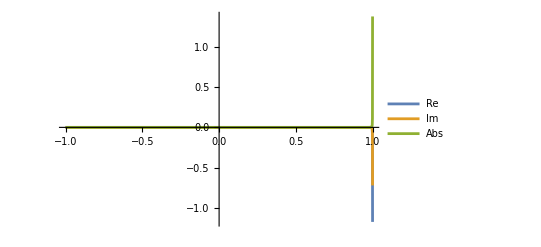

```mathematica
projTest=makeAngularProjector[-2,ellUse,mUse,128];

dataInt=angularIntegrandSamples[TTeukMinus2Compiled,projTest,Xmid];

ListLinePlot[{dataInt["Data"][[All,{1,2}]],dataInt["Data"][[All,{1,3}]],dataInt["Data"][[All,{1,4}]]},PlotLegends->{"Re","Im","Abs"},PlotRange->All]
```

```mathematica
projTest=makeAngularProjector[-2,ellUse,mUse,24];

Keys[projTest]

{Min[projTest["yGrid"]],Max[projTest["yGrid"]],Min[projTest["YGrid"]],Max[projTest["YGrid"]]}
```

{s,ell,m,omega,yGrid,YGrid,Weights,SpheroidalValues,Projector}

{-0.995187,0.995187,-9.95187,9.95187}

```mathematica
ClearAll[Tspy];

Tspy[x_?NumericQ,Y_?NumericQ]:=Sow[Y];

Reap[projectTeukSourceAtXGL[Tspy,projTest][First[patchLeft["XGrid"]]]][[2,1]]//MinMax
```

{-9.95187,9.95187}

```mathematica
convMinus2Left=runAngularProjectionConvergence[TTeukMinus2Compiled,-2,ellUse,mUse,patchLeft["XGrid"],{24,32,48,64}];

vals24=convMinus2Left["ValuesByNY"][24];
vals32=convMinus2Left["ValuesByNY"][32];
vals48=convMinus2Left["ValuesByNY"][48];
vals64=convMinus2Left["ValuesByNY"][64];

convergencePairErrorsInterior[{vals24,vals32,vals48,vals64}]
```

{{0.000394809,0.337721},{0.000819179,0.412383},{0.00083126,0.295117}}

```mathematica
nYListTest2={64,96,128,192};

convMinus2Left2=runAngularProjectionConvergence[TTeukMinus2Compiled,-2,ellUse,mUse,patchLeft["XGrid"],nYListTest2];

convMinus2Left2["PairwiseErrors"]
```

<|{64,96}→<|MaxAbsDifference→0.00169264,RelativeMaxDifference→0.371191|>,{96,128}→<|MaxAbsDifference→0.00169355,RelativeMaxDifference→0.27083|>,{128,192}→<|MaxAbsDifference→0.00338841,RelativeMaxDifference→0.35145|>|>

```mathematica
(* exclude the radial endpoints *)
```

```mathematica
ClearAll[dropRadialEndpoints,convergencePairErrorsInterior];

dropRadialEndpoints[v_List]:=v[[2;;-2]];

convergencePairErrorsInterior[vals_List]:=Module[{pairs,diffs,rels},pairs=Partition[dropRadialEndpoints/@vals,2,1];
diffs=Max[Abs[#2-#1]]&@@@pairs;
rels=Table[diffs[[k]]/Max[Max[Abs[pairs[[k,2]]]],10^-30],{k,Length[pairs]}];
Transpose[{diffs,rels}]];
```

```mathematica
vals24=convMinus2Left["ValuesByNY"][24];
vals32=convMinus2Left["ValuesByNY"][32];
vals48=convMinus2Left["ValuesByNY"][48];
vals64=convMinus2Left["ValuesByNY"][64];

convergencePairErrorsInterior[{vals24,vals32,vals48,vals64}]
```

{{0.000394809,0.337721},{0.000819179,0.412383},{0.00083126,0.295117}}

```mathematica
ClearAll[pointwiseConvergenceTable];

pointwiseConvergenceTable[vals_List,XGrid_List,nYList_List,inds_List]:=Table[Module[{seq,diffs},seq=vals[[All,k]];
diffs=Abs[Differences[seq]];
<|"Index"->k,"X"->XGrid[[k]],"Values"->AssociationThread[nYList,seq],"SuccessiveAbsDiffs"->diffs|>],{k,inds}];

pointwiseConvergenceTable[{vals24,vals32,vals48,vals64},patchLeft["XGrid"],{24,32,48,64},Range[1,6]]
```

{<|Index→1,X→-1.,Values→<|24→-0.000609393-0.000498246 ⅈ,32→-0.000948552-0.000713562 ⅈ,48→-0.00166018-0.00115479 ⅈ,64→-0.00238295-0.00159638 ⅈ|>,SuccessiveAbsDiffs→{0.000401734,0.000837312,0.000846999}|>,<|Index→2,X→-0.950484929106870051022419979242,Values→<|24→-0.000602269-0.000489482 ⅈ,32→-0.000936106-0.000700259 ⅈ,48→-0.00163168-0.00113296 ⅈ,64→-0.00234091-0.00156654 ⅈ|>,SuccessiveAbsDiffs→{0.000394809,0.000819179,0.00083126}|>,<|Index→3,X→-0.811746783480357471594849816978,Values→<|24→-0.000579319-0.000464058 ⅈ,32→-0.000903753-0.000664053 ⅈ,48→-0.00155733-0.00107316 ⅈ,64→-0.00222846-0.00148518 ⅈ|>,SuccessiveAbsDiffs→{0.000381124,0.00077106,0.000787513}|>,<|Index→4,X→-0.611264354373487420572429837736,Values→<|24→-0.000538139-0.000423388 ⅈ,32→-0.000855116-0.00061291 ⅈ,48→-0.00146565-0.000991141 ⅈ,64→-0.00208136-0.00137323 ⅈ|>,SuccessiveAbsDiffs→{0.000369315,0.0007182,0.000724633}|>,<|Index→5,X→-0.388745645626512579427570162264,Values→<|24→-0.000507194-0.000378778 ⅈ,32→-0.000792433-0.000554135 ⅈ,48→-0.00137272-0.000906404 ⅈ,64→-0.00194399-0.00125807 ⅈ|>,SuccessiveAbsDiffs→{0.00033483,0.000678843,0.000670836}|>,<|Index→6,X→-0.18826321651964252840515018302,Values→<|24→-0.000496659-0.00034596 ⅈ,32→-0.000760016-0.000507524 ⅈ,48→-0.00128925-0.000833504 ⅈ,64→-0.00182201-0.00116166 ⅈ|>,SuccessiveAbsDiffs→{0.000308966,0.000621571,0.000625716}|>}

## Quantify endpoint behaviour

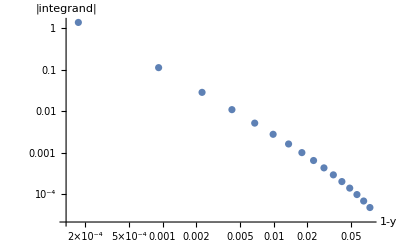

```mathematica
ClearAll[endpointScalingData];

endpointScalingData[data_Association,side_String:"Right",n_Integer:12]:=Module[{d},d=data["Data"];
Which[side==="Right",Transpose[{1-d[[-n;;,1]],d[[-n;;,4]]}],side==="Left",Transpose[{1+d[[1;;n,1]],d[[1;;n,4]]}]]];

rightScale=endpointScalingData[dataInt,"Right",16];

ListLogLogPlot[rightScale,PlotRange->All,AxesLabel->{"1-y","|integrand|"}]
```

```mathematica
ClearAll[makeGaussLegendreRuleCut,makeAngularProjectorCut];

makeGaussLegendreRuleCut[n_Integer,ycut_,wp_:MachinePrecision]:=Module[{gw},gw=GaussianQuadratureWeights[n,-1+ycut,1-ycut,wp];
<|"yGrid"->Nw/@gw[[All,1]],"Weights"->Nw/@gw[[All,2]]|>];

makeAngularProjectorCut[s_Integer,ell_Integer,m_Integer,nY_Integer:96,ycut_:10^-3,wp_:MachinePrecision]:=Module[{omega,rule,yGrid,YGrid,weights,sphVals,projector},omega=m Ω0val;
rule=makeGaussLegendreRuleCut[nY,ycut,wp];
yGrid=rule["yGrid"];
weights=rule["Weights"];
YGrid=YofYCos/@yGrid;
sphVals=Table[SsphY[s,ell,m,omega][y],{y,yGrid}];
projector=2 Pi weights Conjugate[sphVals];
<|"s"->s,"ell"->ell,"m"->m,"omega"->omega,"yGrid"->yGrid,"YGrid"->YGrid,"Weights"->weights,"SpheroidalValues"->sphVals,"Projector"->projector|>];
```

```mathematica
convMinus2LeftCut=Association@Table[nY->projectTeukSourceOnXGridGL[TTeukMinus2Compiled,patchLeft["XGrid"],makeAngularProjectorCut[-2,ellUse,mUse,nY,10^-3]],{nY,{24,32,48,64}}];

convergencePairErrorsInterior[convMinus2LeftCut/@{24,32,48,64}]
```

{{0.000166086,0.229722},{0.000175827,0.195841},{0.0000629821,0.0655941}}

```mathematica
ClearAll[makeGaussLegendreRuleCut,makeAngularProjectorCut];

makeGaussLegendreRuleCut[n_Integer,ycut_,wp_:MachinePrecision]:=Module[{gw},gw=GaussianQuadratureWeights[n,-1+ycut,1-ycut,wp];
<|"yGrid"->Nw/@gw[[All,1]],"Weights"->Nw/@gw[[All,2]]|>];

makeAngularProjectorCut[s_Integer,ell_Integer,m_Integer,nY_Integer:96,ycut_:10^-3,wp_:MachinePrecision]:=Module[{omega,rule,yGrid,YGrid,weights,sphVals,projector},omega=m Ω0val;
rule=makeGaussLegendreRuleCut[nY,ycut,wp];
yGrid=rule["yGrid"];
weights=rule["Weights"];
YGrid=YofYCos/@yGrid;
sphVals=Table[SsphY[s,ell,m,omega][y],{y,yGrid}];
projector=2 Pi weights Conjugate[sphVals];
<|"s"->s,"ell"->ell,"m"->m,"omega"->omega,"yGrid"->yGrid,"YGrid"->YGrid,"Weights"->weights,"SpheroidalValues"->sphVals,"Projector"->projector|>];
```

```mathematica
convMinus2LeftCut=Association@Table[nY->projectTeukSourceOnXGridGL[TTeukMinus2Compiled,patchLeft["XGrid"],makeAngularProjectorCut[-2,ellUse,mUse,nY,10^-3]],{nY,{24,32,48,64}}];

convergencePairErrorsInterior[convMinus2LeftCut/@{24,32,48,64}]
```

{{0.000166086,0.229722},{0.000175827,0.195841},{0.0000629821,0.0655941}}

```mathematica
ClearAll[smoothCompactBump,angularWindowY];

smoothCompactBump[u_?NumericQ]:=If[Abs[u]<1,Exp[-1/(1-u^2)],0];

angularWindowY[Y_?NumericQ,Ymax_?NumericQ]:=smoothCompactBump[Y/Ymax]/smoothCompactBump[0];

YmaxTest=0.7 r0val;

TTeukMinus2Windowed[x_?NumericQ,Y_?NumericQ]:=TTeukMinus2Compiled[x,Y] angularWindowY[Y,YmaxTest];
```

```mathematica
convMinus2LeftWindowed=runAngularProjectionConvergence[TTeukMinus2Windowed,-2,ellUse,mUse,patchLeft["XGrid"],{24,32,48,64}];

convMinus2LeftWindowed["PairwiseErrors"]
```

<|{24,32}→<|MaxAbsDifference→0.0000184045,RelativeMaxDifference→0.305489|>,{32,48}→<|MaxAbsDifference→0.0000154943,RelativeMaxDifference→0.234574|>,{48,64}→<|MaxAbsDifference→6.66226×10^-6,RelativeMaxDifference→0.104497|>|>

### Parallelize projections

```mathematica
(* ============================================================*)
(*Coarse parallel projection over {s,ell,patch}*)(* ============================================================*)ClearAll[sourceFunctionForSpin,patchXGridAssoc,projectOneSpinEllPatch,makeProjectionTasks,runProjectionTasksParallel];

sourceFunctionForSpin[s_Integer]:=Switch[s,
-2,TTeukMinus2Compiled,
+2,TTeukPlus2Compiled,
_,Message[sourceFunctionForSpin::badspin,s];$Failed];

patchXGridAssoc=
<|
"Left"->patchLeft["XGrid"],
"Right"->patchRight["XGrid"]
|>;
```

```mathematica
projectOneSpinEllPatch[s_Integer,ell_Integer,m_Integer,patchName_String,XGrid_List,nZ_Integer:96]:=
Module[
{proj,Tfun,vals},
proj=makeAngularProjector[s,ell,m,nZ];
Tfun=sourceFunctionForSpin[s];
vals=projectTeukSourceOnXGridGL[Tfun,XGrid,proj];
{s,ell,patchName}->
<|
"s"->s,
"ell"->ell,
"m"->m,
"omega"->m Ω0val,
"Patch"->patchName,
"XGrid"->XGrid,
"Values"->vals,
"Projector"->proj
|>
];
```

```mathematica
makeProjectionTasks[sList_List,ellList_List,m_Integer,patchAssoc_Association,nZ_Integer:96]:=
Flatten[
Table[
{s,ell,m,patchName,patchAssoc[patchName],nZ},
{s,sList},
{ell,ellList},
{patchName,Keys[patchAssoc]}
],
2
];
```

```mathematica
DistributeDefinitions[
TTeukMinus2Compiled,
TTeukPlus2Compiled,
sourceFunctionForSpin,
makeAngularProjector,
makeGaussLegendreRule,
SsphZ,
SsphThetaPhi,
projectTeukSourceAtXGL,
projectTeukSourceOnXGridGL,
YofZ,
spinval,
r0val,
Ω0val,
Nw
];
```

```mathematica
runProjectionTasksParallel[sList_List,ellList_List,m_Integer,patchAssoc_Association,nZ_Integer:96]:=Module[
{tasks,results},
tasks=makeProjectionTasks[sList,ellList,m,patchAssoc,nZ];
results=ParallelMap[projectOneSpinEllPatch@@#&,tasks];
Association[results]
];
```

```mathematica
mUse = Round[mModeval];

ellListUse =
  Range[
   Max[Abs[mUse], 2],
   Max[Abs[mUse], 2] + 6
   ];

projResults =
  runProjectionTasksParallel[
   {-2, +2},
   ellListUse,
   mUse,
   patchXGridAssoc,
   96
   ];

projResults[{-2,ellUse,"Left"}]["Values"]

projResults[{-2,ellUse,"Right"}]["Values"]

projResults[{+2,ellUse,"Left"}]["Values"]

projResults[{+2,ellUse,"Right"}]["Values"]
```

```mathematica
runProjectionTasksParallelMonitored[sList_List,ellList_List,m_Integer,patchAssoc_Association,nZ_Integer:96]:=Module[
{tasks,submitted,results},
tasks=makeProjectionTasks[sList,ellList,m,patchAssoc,nZ];
submitted=Table[ParallelSubmit[projectOneSpinEllPatch@@task],{task,tasks}];
Monitor[
results=WaitAll[submitted],
Row[{"Finished ",Count[submitted,_?(#["State"]==="Finished"&)]," / ",
Length[submitted]}
]
];
Association[results]
];
```

```mathematica
(* check *)
```

```mathematica
AbsoluteTiming[testBlock=projectOneSpinEllPatch[-2,ellUse,mUse,"Left",patchLeft["XGrid"],32]]
```

### spherical harmonic Y projections

```mathematica
ClearAll[projectTeff$mMode$y];

Options[projectTeff$mMode$y]=
{
"EndpointCutoff"->0,
WorkingPrecision->MachinePrecision,
AccuracyGoal->Automatic,
PrecisionGoal->Automatic,
MaxRecursion->12
};

projectTeff$mMode$y[s_,l_,m_][TeffHead_][X_?NumericQ,opts:OptionsPattern[]]:=
Module[
{eps,wp,acc,prec,maxrec,θ},
eps=OptionValue["EndpointCutoff"];
wp=OptionValue[WorkingPrecision];
acc=OptionValue[AccuracyGoal];
prec=OptionValue[PrecisionGoal];
maxrec=OptionValue[MaxRecursion];
(* Nintegration local adapative *)
2 Pi NIntegrate[
TeffHead[m][X,-r0val y]*
Conjugate[SpinWeightedSphericalHarmonicY[s,l,m,ArcCos[y],Nw@0]],
{y,-1+eps,1-eps},
Method->{"LocalAdaptive","SymbolicProcessing"->0},
WorkingPrecision->wp,
AccuracyGoal->acc,
PrecisionGoal->prec,
MaxRecursion->maxrec]
];
```

```mathematica
projectTeff$mModerθ[0,0,0][Teffmmb$MMode$XY$numeric][10.3]
```

NIntegrate::precw: The precision of the argument function (((0.00306039 ((416322. LegendreP[-3.5,Power[«2»] Plus[«2»] Power[«2»]])/((27.735+Times[«2»])^(7/4) (219.735+Times[«2»])^(7/4))+(«19» «1»)/((«1»)^(«1») «1»)+«8»+(«1»)/(«1»)+5.2664 («1»))+«18»+«1») «1»)/(2 √π)) is less than WorkingPrecision (20.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in θ near {θ} = {1.401905445255650046718473635866701138031586812273168448414024870721835×10^-10}. NIntegrate obtained 2.108601870730566869678763688261547637874861798973914962244178359843924×10^-8 and 6.139340969559439423851799993786378952219932633674710372553711197265402×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in θ near {θ} = {1.126702878396919367269899805068481198644439622340083146315908897065207×10^-6}. NIntegrate obtained 1.314477796137380528607327173416483216389469324327474800423397776035943×10^-17 and 4.85801066853398873662822119442937266566803293466156571960274934250682×10^-35 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in θ near {θ} = {1.126702880402338138136553983497351730500878272237738448966937830526649×10^-6}. NIntegrate obtained 3.814763143220890277994838585410784335079768163297607134046334546737265×10^-17 and 2.518377181746498142880135915827969704427891032763026793797816394643938×10^-34 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

## C++ code Generator

```mathematica
ClearAll[componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles,flagBits,normalizeMetricSignature,buildFlags];

componentIDs=<|"ll"->0,"ln"->1,"lm"->2,"lmb"->3,"nn"->4,"nm"->5,"nmb"->6,"mm"->7,"mmb"->8|>;

patchIDs=<|"left"->0,"right"->1|>;

yStorageIDs=<|"Full"->0,"HalfWithEvenReflection"->1|>;

magicBytes=Join[ToCharacterCode["GHZSRC1"],{0}];

(*flag bit masks*)
flagBits=<|"NegativeMIsConjugate"->1,(*bit 0*)"MostlyPlusSignature"->2    (*bit 1*)|>;

normalizeMetricSignature[s_]:=Which[s==="MostlyMinus"||s==="-+++"||s==="minus","MostlyMinus",s==="MostlyPlus"||s==="+---"||s==="plus","MostlyPlus",True,$Failed];

buildFlags[negM_,metricSig_]:=Module[{flags=0,sig=normalizeMetricSignature[metricSig]},If[sig===$Failed,Return[$Failed]];
If[TrueQ[negM],flags=BitOr[flags,flagBits["NegativeMIsConjugate"]]];
If[sig==="MostlyPlus",flags=BitOr[flags,flagBits["MostlyPlusSignature"]]];
flags];

teffFuncs=<|"ll"->Teffll$MMode$XY$numeric,"ln"->Teffln$MMode$XY$numeric,"lm"->Tefflm$MMode$XY$numeric,"lmb"->Tefflmb$MMode$XY$numeric,"nn"->Teffnn$MMode$XY$numeric,"nm"->Teffnm$MMode$XY$numeric,"nmb"->Teffnmb$MMode$XY$numeric,"mm"->Teffmm$MMode$XY$numeric,"mmb"->Teffmmb$MMode$XY$numeric|>;

flattenComplexInterleaved[data_?MatrixQ]:=Flatten[({Re[#],Im[#]}&)/@Flatten[data]];

buildComponentMatrix[fun_,m_Integer?NonNegative,XGrid_List,YGrid_List]:=Table[fun[m][x,y],{x,XGrid},{y,YGrid}];

Options[exportBinaryComponentFile]={"YStorage"->"Full","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyMinus"};

exportBinaryComponentFile[file_String,component_String,m_Integer?NonNegative,patch_String,XGrid_List,YGrid_List,data_?MatrixQ,rp_,B_,OptionsPattern[]]:=Module[{nx,ny,stream,flat,patchID,yStorageID,flags,metricSig},nx=Length[XGrid];
ny=Length[YGrid];
If[!KeyExistsQ[componentIDs,component],Return[$Failed]];
If[!KeyExistsQ[patchIDs,patch],Return[$Failed]];
If[!KeyExistsQ[yStorageIDs,OptionValue["YStorage"]],Return[$Failed]];
If[Dimensions[data]=!={nx,ny},Print["Dimension mismatch in exportBinaryComponentFile for ",file];
Return[$Failed];];
metricSig=normalizeMetricSignature[OptionValue["MetricSignature"]];
If[metricSig===$Failed,Print["Invalid MetricSignature option in exportBinaryComponentFile for ",file];
Return[$Failed];];
patchID=patchIDs[patch];
yStorageID=yStorageIDs[OptionValue["YStorage"]];
flags=buildFlags[OptionValue["NegativeMIsConjugate"],metricSig];
If[flags===$Failed,Return[$Failed]];
flat=N[flattenComplexInterleaved[data],17];
stream=OpenWrite[file,BinaryFormat->True];
BinaryWrite[stream,magicBytes,"Byte"];
BinaryWrite[stream,1,"UnsignedInteger32"];(*layout unchanged*)BinaryWrite[stream,m,"Integer32"];
BinaryWrite[stream,componentIDs[component],"UnsignedInteger32"];
BinaryWrite[stream,patchID,"UnsignedInteger32"];
BinaryWrite[stream,yStorageID,"UnsignedInteger32"];
BinaryWrite[stream,flags,"UnsignedInteger32"];
BinaryWrite[stream,N[rp,17],"Real64"];
BinaryWrite[stream,N[B,17],"Real64"];
BinaryWrite[stream,nx,"UnsignedInteger64"];
BinaryWrite[stream,ny,"UnsignedInteger64"];
BinaryWrite[stream,N[XGrid,17],"Real64"];
BinaryWrite[stream,N[YGrid,17],"Real64"];
BinaryWrite[stream,flat,"Real64"];
Close[stream];
file];

Options[exportPatchBinaryFiles]={"Prefix"->"Teff","YStorage"->"Full","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyMinus","Verbose"->False};

exportPatchBinaryFiles[dir_String,m_Integer?NonNegative,patch_String,XGrid_List,YGrid_List,rp_,B_,OptionsPattern[]]:=Module[{prefix,yStorage,negm,metricSig,verbose,data,file},prefix=OptionValue["Prefix"];
yStorage=OptionValue["YStorage"];
negm=OptionValue["NegativeMIsConjugate"];
metricSig=OptionValue["MetricSignature"];
verbose=TrueQ[OptionValue["Verbose"]];
If[!MemberQ[{"left","right"},patch],Return[$Failed]];
CreateDirectory[dir,CreateIntermediateDirectories->True];
KeyValueMap[(If[verbose,Print["Writing ",#1,"  m=",m,"  patch=",patch,"  signature=",metricSig]];
data=buildComponentMatrix[#2,m,XGrid,YGrid];
file=FileNameJoin[{dir,StringTemplate["``_``_m``_``.bin"][prefix,#1,m,patch]}];
exportBinaryComponentFile[file,#1,m,patch,XGrid,YGrid,data,rp,B,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig])&,teffFuncs]];

Options[exportTwoPatchModeBinaryFiles]=Options[exportPatchBinaryFiles];

exportTwoPatchModeBinaryFiles[dir_String,m_Integer?NonNegative,XLeftGrid_List,XRightGrid_List,YGrid_List,rp_,B_,OptionsPattern[]]:=Module[{prefix,yStorage,negm,metricSig,verbose},prefix=OptionValue["Prefix"];
yStorage=OptionValue["YStorage"];
negm=OptionValue["NegativeMIsConjugate"];
metricSig=OptionValue["MetricSignature"];
verbose=TrueQ[OptionValue["Verbose"]];
If[verbose,Print["=== Exporting mode m = ",m,"  signature=",metricSig," ==="]];
exportPatchBinaryFiles[dir,m,"left",XLeftGrid,YGrid,rp,B,"Prefix"->prefix,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig,"Verbose"->verbose];
exportPatchBinaryFiles[dir,m,"right",XRightGrid,YGrid,rp,B,"Prefix"->prefix,"YStorage"->yStorage,"NegativeMIsConjugate"->negm,"MetricSignature"->metricSig,"Verbose"->verbose];];
```

```mathematica
(* usage exportTwoPatchModeBinaryFiles[dir,m,XLeftGrid,XRightGrid,YGrid,rp,B,"MetricSignature"->"MostlyPlus","Verbose"->True] *)
```

```mathematica
XLeftGrid={-2.,-1.};
XRightGrid={1.,2.};
YHalfGrid={0.,1.,2.};

Do[exportTwoPatchModeBinaryFiles["TeffBinary",m,XLeftGrid,XRightGrid,YHalfGrid,r0val,Bval,"Prefix"->"Teff","YStorage"->"HalfWithEvenReflection","NegativeMIsConjugate"->True,"MetricSignature"->"MostlyPlus","Verbose"->True],{m,0,30}];
```

=== Exporting mode m = 0 ===

Writing ll  m=0  patch=left

Writing ln  m=0  patch=left

Writing lm  m=0  patch=left

Writing lmb  m=0  patch=left

Writing nn  m=0  patch=left

Writing nm  m=0  patch=left

Writing nmb  m=0  patch=left

Writing mm  m=0  patch=left

Writing mmb  m=0  patch=left

CreateDirectory::eexist: /Users/antares/TeffBinary already exists.

Writing ll  m=0  patch=right

Writing ln  m=0  patch=right

Writing lm  m=0  patch=right

Writing lmb  m=0  patch=right

Writing nn  m=0  patch=right

Writing nm  m=0  patch=right

Writing nmb  m=0  patch=right

Writing mm  m=0  patch=right

Writing mmb  m=0  patch=right

=== Exporting mode m = 1 ===

CreateDirectory::eexist: /Users/antares/TeffBinary already exists.

Writing ll  m=1  patch=left

Writing ln  m=1  patch=left

Writing lm  m=1  patch=left

Writing lmb  m=1  patch=left

Writing nn  m=1  patch=left

Writing nm  m=1  patch=left

Writing nmb  m=1  patch=left

Writing mm  m=1  patch=left

Writing mmb  m=1  patch=left

CreateDirectory::eexist: /Users/antares/TeffBinary already exists.

General::stop: Further output of CreateDirectory::eexist will be suppressed during this calculation.

Writing ll  m=1  patch=right

Writing ln  m=1  patch=right

Writing lm  m=1  patch=right

Writing lmb  m=1  patch=right

Writing nn  m=1  patch=right

Writing nm  m=1  patch=right

Writing nmb  m=1  patch=right

Writing mm  m=1  patch=right

Writing mmb  m=1  patch=right

=== Exporting mode m = 2 ===

Writing ll  m=2  patch=left

Writing ln  m=2  patch=left

Writing lm  m=2  patch=left

Writing lmb  m=2  patch=left

Writing nn  m=2  patch=left

Writing nm  m=2  patch=left

Writing nmb  m=2  patch=left

Writing mm  m=2  patch=left

Writing mmb  m=2  patch=left

Writing ll  m=2  patch=right

Writing ln  m=2  patch=right

Writing lm  m=2  patch=right

Writing lmb  m=2  patch=right

Writing nn  m=2  patch=right

Writing nm  m=2  patch=right

Writing nmb  m=2  patch=right

Writing mm  m=2  patch=right

Writing mmb  m=2  patch=right

=== Exporting mode m = 3 ===

Writing ll  m=3  patch=left

Writing ln  m=3  patch=left

Writing lm  m=3  patch=left

Writing lmb  m=3  patch=left

Writing nn  m=3  patch=left

Writing nm  m=3  patch=left

Writing nmb  m=3  patch=left

Writing mm  m=3  patch=left

Writing mmb  m=3  patch=left

Writing ll  m=3  patch=right

Writing ln  m=3  patch=right

Writing lm  m=3  patch=right

Writing lmb  m=3  patch=right

Writing nn  m=3  patch=right

Writing nm  m=3  patch=right

Writing nmb  m=3  patch=right

Writing mm  m=3  patch=right

Writing mmb  m=3  patch=right

=== Exporting mode m = 4 ===

Writing ll  m=4  patch=left

Writing ln  m=4  patch=left

Writing lm  m=4  patch=left

Writing lmb  m=4  patch=left

Writing nn  m=4  patch=left

Writing nm  m=4  patch=left

Writing nmb  m=4  patch=left

Writing mm  m=4  patch=left

Writing mmb  m=4  patch=left

Writing ll  m=4  patch=right

Writing ln  m=4  patch=right

Writing lm  m=4  patch=right

Writing lmb  m=4  patch=right

Writing nn  m=4  patch=right

Writing nm  m=4  patch=right

Writing nmb  m=4  patch=right

Writing mm  m=4  patch=right

Writing mmb  m=4  patch=right

=== Exporting mode m = 5 ===

Writing ll  m=5  patch=left

Writing ln  m=5  patch=left

Writing lm  m=5  patch=left

Writing lmb  m=5  patch=left

Writing nn  m=5  patch=left

Writing nm  m=5  patch=left

Writing nmb  m=5  patch=left

Writing mm  m=5  patch=left

Writing mmb  m=5  patch=left

Writing ll  m=5  patch=right

Writing ln  m=5  patch=right

Writing lm  m=5  patch=right

Writing lmb  m=5  patch=right

Writing nn  m=5  patch=right

Writing nm  m=5  patch=right

Writing nmb  m=5  patch=right

Writing mm  m=5  patch=right

Writing mmb  m=5  patch=right

=== Exporting mode m = 6 ===

Writing ll  m=6  patch=left

Writing ln  m=6  patch=left

Writing lm  m=6  patch=left

Writing lmb  m=6  patch=left

Writing nn  m=6  patch=left

Writing nm  m=6  patch=left

Writing nmb  m=6  patch=left

Writing mm  m=6  patch=left

Writing mmb  m=6  patch=left

Writing ll  m=6  patch=right

Writing ln  m=6  patch=right

Writing lm  m=6  patch=right

Writing lmb  m=6  patch=right

Writing nn  m=6  patch=right

Writing nm  m=6  patch=right

Writing nmb  m=6  patch=right

$Aborted

```mathematica
teffSourceSymbols={Teffll$MMode$XY$numeric,Teffln$MMode$XY$numeric,Tefflm$MMode$XY$numeric,Tefflmb$MMode$XY$numeric,Teffnn$MMode$XY$numeric,Teffnm$MMode$XY$numeric,Teffnmb$MMode$XY$numeric,Teffmm$MMode$XY$numeric,Teffmmb$MMode$XY$numeric};

generatorSymbols={componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles};Save["TeffSources.wl",teffSourceSymbols];
Save["TeffBinaryGenerator.wl",generatorSymbols];
```

```mathematica
DumpSave["TeffSources.mx",{Teffll$MMode$XY$numeric,Teffln$MMode$XY$numeric,Tefflm$MMode$XY$numeric,Tefflmb$MMode$XY$numeric,Teffnn$MMode$XY$numeric,Teffnm$MMode$XY$numeric,Teffnmb$MMode$XY$numeric,Teffmm$MMode$XY$numeric,Teffmmb$MMode$XY$numeric}]
```

```mathematica
Save["TeffBinaryGenerator.wl",{componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles}]
```

```mathematica
Save["TeffBinaryGeneratorWithSources.wl",{componentIDs,patchIDs,yStorageIDs,magicBytes,teffFuncs,flattenComplexInterleaved,buildComponentMatrix,exportBinaryComponentFile,exportPatchBinaryFiles,exportTwoPatchModeBinaryFiles,Teffll$MMode$XY$numeric,Teffln$MMode$XY$numeric,Tefflm$MMode$XY$numeric,Tefflmb$MMode$XY$numeric,Teffnn$MMode$XY$numeric,Teffnm$MMode$XY$numeric,Teffnmb$MMode$XY$numeric,Teffmm$MMode$XY$numeric,Teffmmb$MMode$XY$numeric}]
```

WolframAlphaQueryResults